```mathematica
Simplify[(x-1)^2+(y-1)^2==2(x-3)^2+2(y-4)^2]
```

48+x^2+y^2==10 x+14 y

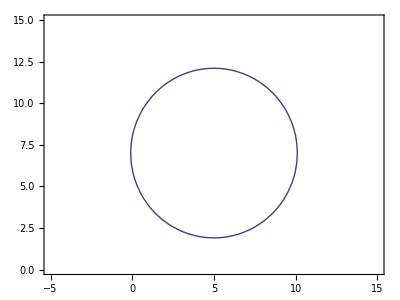

```mathematica
ContourPlot[48+x^2+y^2==10 x+14 y,{x,-5,15},{y,0,15},AspectRatio->Automatic]
```

```mathematica
Manipulate[Plot[m x+4,{x,-10,10},PlotRange->{-0,10},AspectRatio->Automatic],{m,0,4,0.1}]
```

```mathematica
Manipulate[Plot[ x^3+b x^2+x+1,{x,-10,10},PlotRange->{-0,10},AspectRatio->Automatic],{b,-10,10,1 }]
```

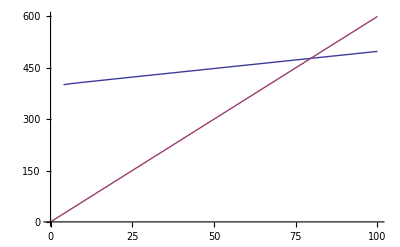

```mathematica
Needs["PlotLegends`"]
Plot[{400+√(x(x-4)),6x},{x,0,100} ,PlotLegend->{"400+√(x (x - 4))", "6x"},LegendPosition->{1,0},  LegendTextSpace->5]
```

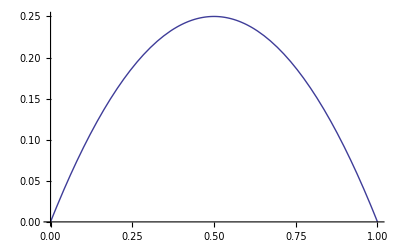

```mathematica
Plot[x-x^2,{x,0,1} ]
```

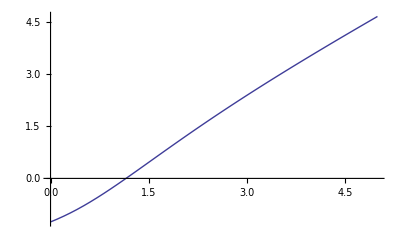

```mathematica
Plot[(x^3+3x-5)/(x^2+4),{x,0,5} ]
```

```mathematica
f[x_]:= (x^3+3x-5)/(x^2+4)
Table[f[i],{i,-4,4}]
```

{-81/20,-41/13,-19/8,-9/5,-5/4,-1/5,9/8,31/13,71/20}

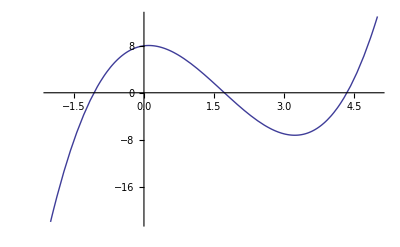

```mathematica
Plot[x^3-5 x^2+ x+8,{x,-2,5} ]
```

```mathematica
f[x_]:= (a x+b)/(c x-a)
f[f[x]]
```

(b+(a (b+a x))/(-a+c x))/(-a+(c (b+a x))/(-a+c x))

{1.2 Abs[x],0.5 Abs[x],0.2 Abs[x]}

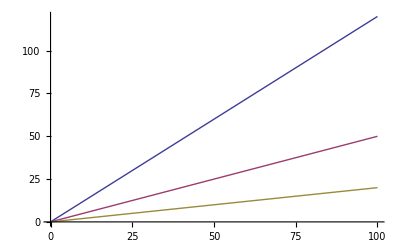

```mathematica
Table[Abs[k x],{k,{1.2,0.5,0.2}}]
Plot[%,{x,0,100}]
```

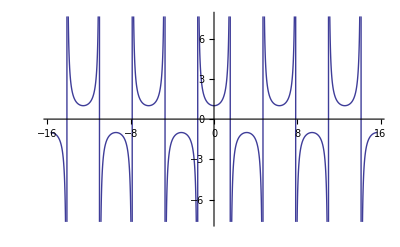

```mathematica
Plot[Sec[x],{x, -5Pi, 5Pi}]
```

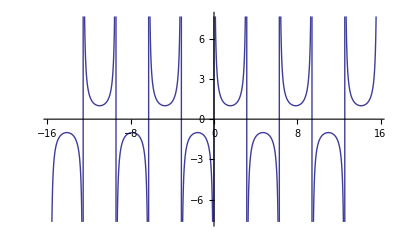

```mathematica
Plot[Csc[x],{x, -5Pi, 5Pi}]
```

```mathematica
(n+1)^4-n^4//Expand
```

1+4 n+6 n^2+4 n^3

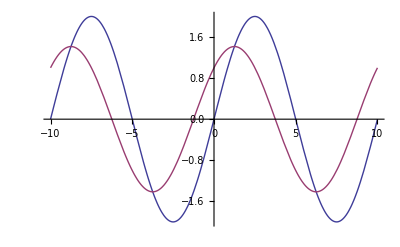

```mathematica
Plot[{2 Sin[(π t)/5],Sin[(π t)/5]+Cos[(π t)/5]},{t,-10,10}]
```

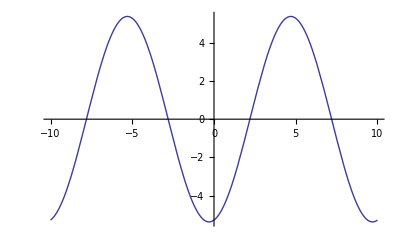

```mathematica
Plot[3Sin[(π t)/5]-5Cos[(π t)/5]+2Sin[(π t)/5-3],{t,-10,10}]
```

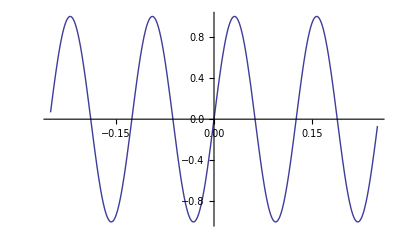

```mathematica
Plot[Sin[ 50t],{t,-0.25,0.25}]
```

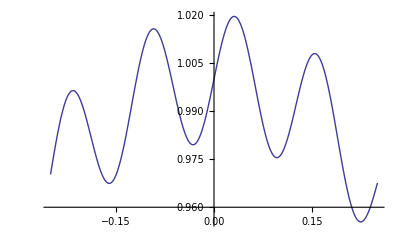

```mathematica
Plot[Cos[t]+1/50 Sin[ 50t],{t,-0.25,0.25}]
```

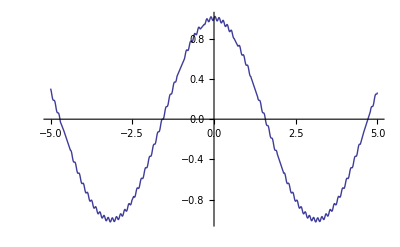

```mathematica
Plot[Cos[t]+1/50 Sin[ 50t],{t,-5,5}]
```

```mathematica
D [(Tan[x]-1)^2,{x,2}]
```

2 Sec[x]^4+4 Sec[x]^2 (-1+Tan[x]) Tan[x]

```mathematica
Factor[x^4-4 x^3+x^2+2x+12]
```

(-3+x) (-4-2 x-x^2+x^3)

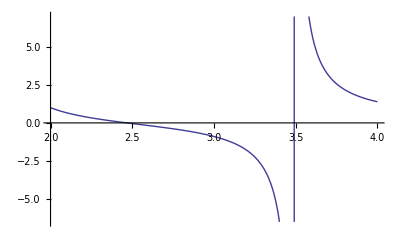

```mathematica
Plot[(-4-2 x-x^2+x^3)/(x^4-4 x^3+x^2+ x+6),{x,2,4}]
```

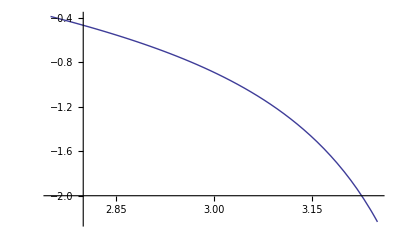

```mathematica
Plot[(-4-2 x-x^2+x^3)/(x^4-4 x^3+x^2+ x+6),{x,2.75,3.25},PlotRange->Full]
```

```mathematica
Limit[(1/2 Sin[x]Cos[x])/(1/2 x-1/2 Sin[x]Cos[x]),x->0,Direction->-1]
```

∞

```mathematica
Piecewise
```

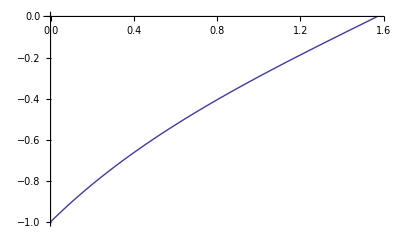

```mathematica
Plot[Tan[x]-Sec[x] ,{x,0,π/2}]
```

```mathematica
Tan[π/2-0.01]-Sec[π/2-0.01]
```

-0.00500004

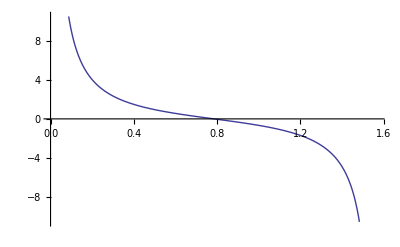

```mathematica
Plot[Csc[x]-Sec[x] ,{x,0,π/2}]
```

{-1-x+2 x^2,-1-2 x+2 x^2,-1-3 x+2 x^2,-1-4 x+2 x^2}

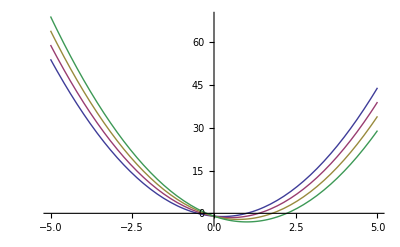

```mathematica
Table[2 x^2-c x-1,{c,{1,2,3,4}}]
Plot[%,{x,-5,5}]
```

```mathematica
D[Tan[2x],{x,4}]
```

256 Sec[2 x]^4 Tan[2 x]+128 Sec[2 x]^2 Tan[2 x]^3

```mathematica
D[-10 √Abs[x y],x]
```

-(5 y Abs'[x y])/(√Abs[x y])

4.4-29

```mathematica
D[(√(a^2+x^2))/Subscript[c, 1]+(√(b^2+(d-x)^2))/Subscript[c, 2],x]
```

x/(√(a^2+x^2) c_1)-(d-x)/(√(b^2+(d-x)^2) c_2)

4.4-18

```mathematica
Solve[b^2 x^2+a^2 y^2==a^2 b^2,y]
```

{{y→-(√(a^2 b^2-b^2 x^2))/a},{y→(√(a^2 b^2-b^2 x^2))/a}}

```mathematica
D[(√(a^2 b^2-b^2 x^2))/a,x]
```

-(b^2 x)/(a √(a^2 b^2-b^2 x^2))

```mathematica
Solve[(0-(√(a^2 b^2-b^2 Subscript[x, 0]^2))/a)==(b^2 Subscript[x, 0])/(a √(a^2 b^2-b^2 Subscript[x, 0]^2))(Subscript[x, 1]-Subscript[x, 0]),Subscript[x, 1]]
```

{{x_1→(-a^2+2 x_0^2)/x_0}}

```mathematica
Solve[(y-(√(a^2 b^2-b^2 Subscript[x, 0]^2))/a)==(b^2 Subscript[x, 0])/(a √(a^2 b^2-b^2 Subscript[x, 0]^2))(0-Subscript[x, 0]),y]
```

{{y→(a^2 b^2-2 b^2 x_0^2)/(a √(b^2 (a^2-x_0^2)))}}

```mathematica
1/2(-a^2+2 Subscript[x, 0]^2)/Subscript[x, 0](a^2 b^2-2 b^2 Subscript[x, 0]^2)/(a √(b^2 (a^2-Subscript[x, 0]^2)))//Simplify
```

-(b^2 (a^2-2 x_0^2)^2)/(2 a x_0 √(b^2 (a^2-x_0^2)))

```mathematica
Solve[D[-(b^2 (a^2-2 Subscript[x, 0]^2)^2)/(2 a Subscript[x, 0] √(b^2 (a^2-Subscript[x, 0]^2))),Subscript[x, 0]]==0,Subscript[x, 0]]
```

{{x_0→-a/(√2)},{x_0→a/(√2)},{x_0→-√(a^2/2+a^2/(√2))},{x_0→√(a^2/2+a^2/(√2))},{x_0→-(√(a^2-√2 a^2))/(√2)},{x_0→(√(a^2-√2 a^2))/(√2)}}

```mathematica
Solve[D[(√(a^2 b^2-b^2 x^2))/a x,x]==0,x]
```

{{x→-a/(√2)},{x→a/(√2)}}

4.4-35

```mathematica
Solve[D[3*5(3^2+5^2-2*3*5Cos[θ])^(-1/2)Sin[θ],θ]==0,θ]
```

Solve::verif: Potential solution {θ → ComplexInfinity} (possibly discarded by verifier) should be checked by hand. May require use of limits.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[3/5]},{θ→ArcCos[3/5]},{θ→-ArcCos[5/3]},{θ→ArcCos[5/3]}}

```mathematica
Solve[D[h*m(h^2+m^2-2*h*m Cos[θ])^(-1/2)Sin[θ],θ]==0,θ]
```

Solve::verif: Potential solution {θ → ComplexInfinity} (possibly discarded by verifier) should be checked by hand. May require use of limits.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[h/m]},{θ→ArcCos[h/m]},{θ→-ArcCos[m/h]},{θ→ArcCos[m/h]}}

```mathematica
(Subscript[y, 0]/(Subscript[x, 0]-p)-(2p)/Subscript[y, 0])/(1+Subscript[y, 0]/(Subscript[x, 0]-p)(2p)/Subscript[y, 0])//Simplify
```

```mathematica
(2 p^2-2 p Subscript[x, 0]+4p Subscript[x, 0])/((p+Subscript[x, 0]) Subscript[y, 0])
```

```mathematica
(2 p^2-2 p Subscript[x, 0]+4p Subscript[x, 0])/((p+Subscript[x, 0]) Subscript[y, 0])//Simplify
```

(2 p)/y_0

4.9-1

```mathematica
((a+b+c)/3)^3-abc//Expand
```

a^3/27-abc+(a^2 b)/9+(a b^2)/9+b^3/27+(a^2 c)/9+(2 a b c)/9+(b^2 c)/9+(a c^2)/9+(b c^2)/9+c^3/27

```mathematica
Solve[2π r^2+2π r h==c,h]
```

{{h→(c-2 π r^2)/(2 π r)}}

```mathematica
D[π r^2(c-2 π r^2)/(2 π r),r]
```

-2 π r^2+1/2 (c-2 π r^2)

```mathematica
Solve[D[π r^2(c-2 π r^2)/(2 π r),r]==0,r]
```

{{r→-(√c)/(√(6 π))},{r→(√c)/(√(6 π))}}

Tech4.1

```mathematica
x/(√(a^2+x^2) Subscript[c, 1])-(d-x)/(√(b^2+(d-x)^2) Subscript[c, 2])==0//Simplify
```

x/(√(a^2+x^2) c_1)+(-d+x)/(√(b^2+(d-x)^2) c_2)==0

```mathematica
(x/(√(a^2+x^2) Subscript[c, 1]))^2==((d-x)/(√(b^2+(d-x)^2) Subscript[c, 2]))^2//Simplify
```

x^2/((a^2+x^2) c_1^2)==(d-x)^2/((b^2+(d-x)^2) c_2^2)

```mathematica
x^2(b^2+(d-x)^2) Subscript[c, 2]^2==(a^2+x^2) Subscript[c, 1]^2(d-x)^2//Expand
```

b^2 x^2 c_2^2+d^2 x^2 c_2^2-2 d x^3 c_2^2+x^4 c_2^2==a^2 d^2 c_1^2-2 a^2 d x c_1^2+a^2 x^2 c_1^2+d^2 x^2 c_1^2-2 d x^3 c_1^2+x^4 c_1^2

```mathematica
b^2 x^2 Subscript[c, 2]^2+d^2 x^2 Subscript[c, 2]^2-2 d x^3 Subscript[c, 2]^2+x^4 Subscript[c, 2]^2-a^2 d^2 Subscript[c, 1]^2-2 a^2 d x Subscript[c, 1]^2+a^2 x^2 Subscript[c, 1]^2+d^2 x^2 Subscript[c, 1]^2-2 d x^3 Subscript[c, 1]^2+x^4 Subscript[c, 1]^2
```

((d-x)^2 x^2+a^2 (-d^2-2 d x+x^2)) c_1^2+(b^2+(d-x)^2) x^2 c_2^2

```mathematica
Collect[x^2(b^2+(d-x)^2) Subscript[c, 2]^2-(a^2+x^2) Subscript[c, 1]^2(d-x)^2==0,x,Simplify]
```

-a^2 d^2 c_1^2+2 a^2 d x c_1^2+2 d x^3 (c_1^2-c_2^2)+x^4 (-c_1^2+c_2^2)+x^2 (-(a^2+d^2) c_1^2+(b^2+d^2) c_2^2)==0

Tech4.2

```mathematica
TrigExpand[Sin[7/12 π-x]]
```

1/2 √(3/2) Cos[x]+Cos[x]/(2 √2)+1/2 √(3/2) Sin[x]-Sin[x]/(2 √2)

```mathematica
Sin[x]/Cos[x]^2-TrigExpand[Sin[7/12 π-x]]/TrigExpand[Cos[7/12 π-x]]^2//Simplify
```

-(2 ((√2+√6) Cos[x]+Sin[x] (-2-√2+√3+√6+2 Tan[x]-(2+√3) Tan[x]^2)))/((-1+√3) Cos[x]-(1+√3) Sin[x])^2

10.4 - 32

```mathematica
Log[10^81+1]//N
```

186.509

```mathematica
Log[10^9+1]//N
```

20.7233

10.4 - 32

```mathematica
Sum[1/i,{i,1,10^5}]//N
```

12.0901

10.4 - 35

```mathematica
Integrate[Log[x],x]
```

-x+x Log[x]

```mathematica
15!
```

1307674368000

```mathematica
n=10
n!//N
√(2π*n)(n/ⅇ)^n//N
```

10

3.6288×10^6

3.5987×10^6

5.2 - 50

```mathematica
Integrate[x Sin[x],x]
Integrate[%,x]
Integrate[%,x]
Integrate[%,x]
Integrate[%,x]
Integrate[%,x]
Integrate[%,x]
```

-x Cos[x]+Sin[x]

-2 Cos[x]-x Sin[x]

x Cos[x]-3 Sin[x]

4 Cos[x]+x Sin[x]

-x Cos[x]+5 Sin[x]

-6 Cos[x]-x Sin[x]

x Cos[x]-7 Sin[x]

5.3 - 55

```mathematica
m=50
n=60
Sum[(m-i)(n-i),{i,0,m}]//N
```

50

60

55675.

7.7-61

```mathematica
x=1/4
y=1/4
(x+y)/(1-x y)
```

1/4

1/4

8/15

```mathematica
x=8/15
y=1/4
(x+y)/(1-x y)
```

8/15

1/4

47/52

```mathematica
x=47/52
y=5/99
(x+y)/(1-x y)
```

47/52

5/99

1

10.8

```mathematica
D[ArcTan[x],{x,5}]
```

(384 x^4)/((1+x^2)^5)-(288 x^2)/((1+x^2)^4)+24/((1+x^2)^3)

5.10-6

```mathematica
1/(120π)v∫_(120π ϕ+ϕ)^(120π(ϕ+1)+ϕ) Sin[μ]^2 ⅆμ
```

v/2

```mathematica
∫_0^(2π) Sin[μ]^2 ⅆμ
```

π

Tech5.1

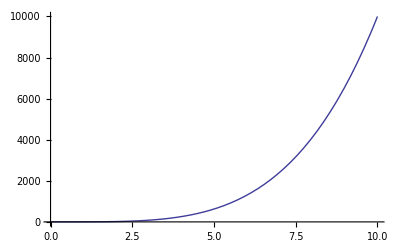

```mathematica
Plot[x^4+1,{x,0,10}]
```

```mathematica
∫_0^5 (x^4+1)ⅆx
```

630

```mathematica
Table[∑_(i=0)^(n-1) 5/n((5/n i)^4+1),{n,{5,10,20,40,80,160,320,640}}]//N
```

{359.,484.156,554.479,591.589,610.632,620.275,625.127,627.561}

```mathematica
Table[∑_(i=0)^(n-1) 5/n((5/n i)^4+1)-630,{n,{5,10,20,40,80,160,320,640}}]//N
```

{-271.,-145.844,-75.5215,-38.4115,-19.3685,-9.72494,-4.87264,-2.43886}

```mathematica
Table[∑_(i=1)^n 5/n((5/n i)^4+1)-630,{n,{5,10,20,40,80,160,320,640}}]//N
```

{354.,166.656,80.7285,39.7135,19.694,9.80631,4.89299,2.44395}

```mathematica
Table[∑_(i=1)^n 5/n((5/n(i-1/2))^4+1)-630,{n,{5,10,20,40,80,160,320,640}}]//N
```

{-20.6875,-5.19922,-1.30151,-0.325485,-0.081378,-0.0203449,-0.00508625,-0.00127157}

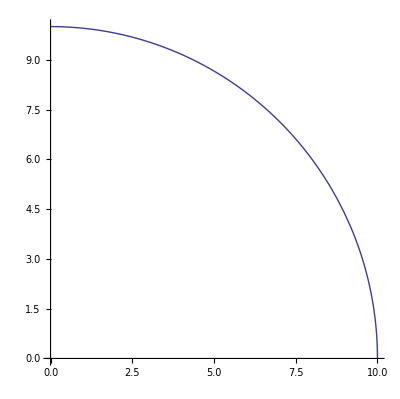

```mathematica
Plot[√(100-x^2),{x,0,10},AspectRatio->Automatic]
```

```mathematica
∫_0^10 √(100-x^2)ⅆx
```

25 π

```mathematica
Table[∑_(i=0)^(n-1) 10/n √(100-(10/n i)^2)-25 π,{n,{5,10,20,40,80,160,320,640}}]//N
```

{7.3864,4.07314,2.17181,1.13388,0.583929,0.297976,0.151115,0.0763093}

```mathematica
Table[∑_(i=1)^n 10/n √(100-(10/n i)^2)-25 π,{n,{5,10,20,40,80,160,320,640}}]//N
```

{-12.6136,-5.92686,-2.82819,-1.36612,-0.666071,-0.327024,-0.161385,-0.0799407}

```mathematica
Table[∑_(i=1)^n 10/n √(100-(10/n(i-1/2))^2)-25 π,{n,{5,10,20,40,80,160,320,640}}]//N
```

{0.759879,0.270469,0.0959484,0.0339802,0.012024,0.00425291,0.00150395,0.000531783}

Tech5.2

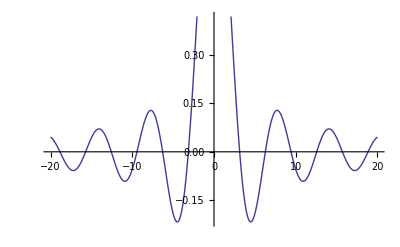

```mathematica
Plot[Sin[x]/x,{x,-20,20}]
```

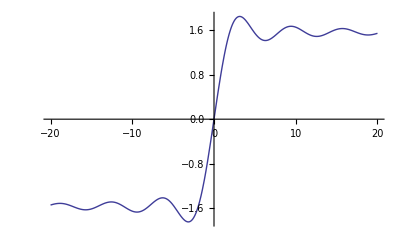

```mathematica
Plot[SinIntegral[x],{x,-20,20}]
```

6.3-19

```mathematica
∫2π x 2 √(b^2-x^2)ⅆx
```

-4/3 π (b^2-x^2)^(3/2)

6.3-21

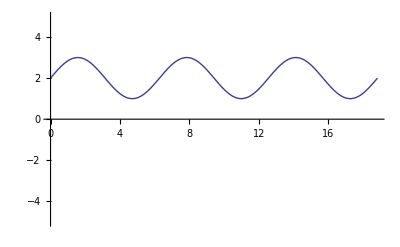

```mathematica
Plot[Sin[x]+2,{x,0,6Pi},PlotRange->{-5,5}]
```

6.3-19

```mathematica
∫Sin[x]^2 ⅆx
```

x/2-1/4 Sin[2 x]

6.3-17

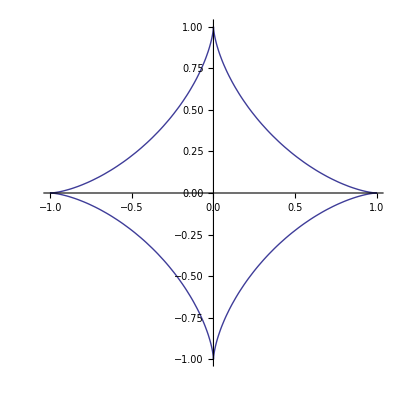

```mathematica
ParametricPlot[{Sin[u]^3,Cos[u]^3},{u,0,2Pi}]
```

6.3-37

```mathematica
Table[∫_0^1 x^i ⅆx,{i,{1,2,4,10,100}}]//N
```

{0.5,0.333333,0.2,0.0909091,0.00990099}

```mathematica
Manipulate[Plot[x^i,{x,0,1}],{i,1,10,1}]
```

6.3-27

```mathematica
∫_0^4 40*62.4(6+x+(40x)/(36π))ⅆx
```

86934.2

Tech6.1

```mathematica
D[√(1-y^2/b^2),y]
```

-y/(b^2 √(1-y^2/b^2))

Tech6.2

```mathematica
∫_-1^1 √(1+(D[√(1-x^2),x])^2)ⅆx
```

π

```mathematica
Table[π-∑_(i=1)^n √((2/n)^2+(√(1-(-1+2/n i)^2)-√(1-(-1+2/n(i-1))^2))^2),{n,{2,4,8,16,32,64,128,256}}]//N
```

{0.313166,0.106316,0.0370966,0.0130483,0.00460298,0.00162571,0.000574489,0.000203063}

```mathematica
∫_-1^1 √(1+x^2/(1-x^2))ⅆx
```

π

7.3-48

```mathematica
Solve[D[(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ),{x,2}]==0,x]
```

{{x→μ-σ},{x→μ+σ}}

7.4-39

```mathematica
2^(1/12)//N
```

1.05946

7.7-61

```mathematica
(47/52+5/99)/(1-47/52*5/99)
```

1

7.7-64

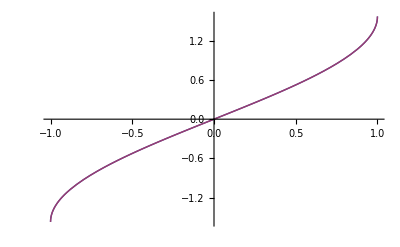

```mathematica
Plot[{ArcSin[x],ArcTan[x/(√(1-x^2))]},{x,-1,1}]
```

7.7-65

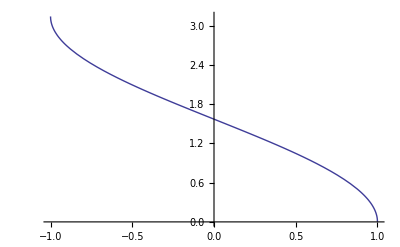

```mathematica
Plot[π/2-ArcSin[x],{x,-1,1}]
```

7.7-66

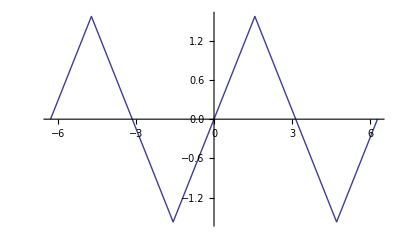

```mathematica
Plot[ArcSin[Sin[x]],{x,-2π,2π}]
```

7.7-71

```mathematica
D[x/2 √(a^2-x^2),x]
D[a^2/2 ArcSin[x/a],x]
```

-x^2/(2 √(a^2-x^2))+1/2 √(a^2-x^2)

a/(2 √(1-x^2/a^2))

7.8-58

```mathematica
D[ArcTan[Sinh[t]],{t,2}]
D[ArcTan[Sinh[t]],{t,2}]//Simplify
```

-(2 Cosh[t]^2 Sinh[t])/((1+Sinh[t]^2)^2)+Sinh[t]/(1+Sinh[t]^2)

-Sech[t] Tanh[t]

```mathematica
2 Cosh[t]^2 Sinh[t]+Sinh[t](1+Sinh[t]^2)//Expand
```

Sinh[t]+2 Cosh[t]^2 Sinh[t]+Sinh[t]^3

7.10-5

```mathematica
Log[2]//N
```

0.693147

```mathematica
(1+0.07)^10
```

2.01375

7.10-13

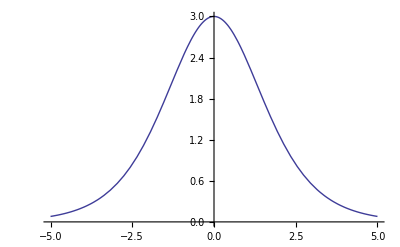

```mathematica
Plot[3 Sech[x/2]^2,{x,-5,5}]
```

Tech7.1

```mathematica
1/(√(2π))∫_0^x ⅇ^(-t^2/2)ⅆt
```

1/2 Erf[x/(√2)]

8.1-70

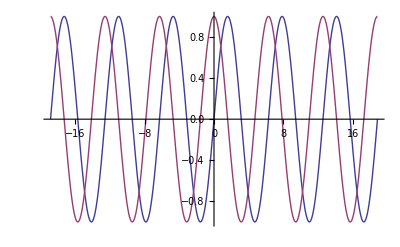

```mathematica
Plot[{Sin[x],Cos[x]},{x,-6Pi,6Pi}]
```

8.2-34

```mathematica
2∫_0^(π/2) π(Sin[x]-k)^2 ⅆx
```

1/2 π (-8 k+π+2 k^2 π)

```mathematica
D[1/2 π (-8 k+π+2 k^2 π),k]
```

1/2 π (-8+4 k π)

```mathematica
1/2 π (-8 k+π+2 k^2 π)/.k->2/π//N
1/2 π (-8 k+π+2 k^2 π)/.k->1//N
1/2 π (-8 k+π+2 k^2 π)/.k->0//N
```

0.934802

2.23804

4.9348

8.5-44

```mathematica
∫1/((y-m)(M-y))ⅆy
```

(-Log[-m+y]+Log[-M+y])/(m-M)

Tech8.1

```mathematica
Integrate[(3x+10)^50,x]
```

1/153 (10+3 x)^51

```mathematica
Integrate[Sin[x]^2 Cos[x]^3,x]
```

Sin[x]/8-1/48 Sin[3 x]-1/80 Sin[5 x]

```mathematica
Integrate[Sin[x]^2 Cos[x]^3,x]//TrigExpand
```

Sin[x]/8-1/16 Cos[x]^2 Sin[x]-1/16 Cos[x]^4 Sin[x]+Sin[x]^3/48+1/8 Cos[x]^2 Sin[x]^3-Sin[x]^5/80

```mathematica
Integrate[√(9 x^2+x^4),x]
```

((x^2 (9+x^2))^(3/2))/(3 x^3)

```mathematica
Integrate[√(9 x^2+x^4),{x,-1,1}]
```

-18+(20 √10)/3

```mathematica
Table[Apart[x^i/(x^2-4)],{i,10}]
```

{1/(2 (-2+x))+1/(2 (2+x)),1+1/(-2+x)-1/(2+x),2/(-2+x)+x+2/(2+x),4+4/(-2+x)+x^2-4/(2+x),8/(-2+x)+4 x+x^3+8/(2+x),16+16/(-2+x)+4 x^2+x^4-16/(2+x),32/(-2+x)+16 x+4 x^3+x^5+32/(2+x),64+64/(-2+x)+16 x^2+4 x^4+x^6-64/(2+x),128/(-2+x)+64 x+16 x^3+4 x^5+x^7+128/(2+x),256+256/(-2+x)+64 x^2+16 x^4+4 x^6+x^8-256/(2+x)}

Tech8.2

```mathematica
Integrate[1/(k y(L-y)), y ]
```

Log[y]/(k L)-Log[-L+y]/(k L)

```mathematica
(Log[y]/(k L)-Log[-L+y]/(k L))-(Log[Subscript[y, 0]]/(k L)-Log[-L+Subscript[y, 0]]/(k L))//Simplify
```

(Log[y]-Log[-L+y]-Log[y_0]+Log[-L+y_0])/(k L)

9.1-27

```mathematica
Limit[(1/2 Sin[x]Cos[x]-1/2 x Cos[x]^2)/(1/2 x-1/2 Sin[x]Cos[x]),x->0,Direction->-1]
```

1/2

9.1-28

```mathematica
Limit[((1-t)^2((4 t^2-t^4)/4))/(((2t-t^2)/2)^2),t->0,Direction->-1]
```

1

```mathematica
Limit[((1-t)^2(4-t^2))/(2-t)^2,t->0,Direction->-1]
```

1

```mathematica
(1-t)^2(4-t^2)//Expand
```

4-8 t+3 t^2+2 t^3-t^4

```mathematica
D[(1-t)^2(4-t^2),t]//Simplify
D[(2-t)^2,t]//Simplify
```

-8+6 t+6 t^2-4 t^3

2 (-2+t)

```mathematica
Limit[(t t^2/2)/(t-√((4 t^2-t^4)/4)),t->0,Direction->-1]
```

4

```mathematica
Limit[t^2/(2-√(4-t^2)),t->0,Direction->-1]
```

4

```mathematica
D[t^2,{t,2}]//Simplify
D[2-√(4-t^2),{t,2}]//Simplify
```

2

4/((4-t^2)^(3/2))

9.1-30

```mathematica
Solve[{ x+y==-1,4x+3y==0},{x,y}]
```

{{x→3,y→-4}}

```mathematica
D[(x-1)Sin[π x],{x,2}]
```

2 π Cos[π x]-π^2 (-1+x) Sin[π x]

9.2-41

```mathematica
N[x^(1/x)/.x->1000000000,50]
```

1.0000000207232660516732861138177439864559779596665

9.2-18

```mathematica
Limit[(Csc[x]^2-1/x^2)^2,x->0]
```

1/9

9.2-42

```mathematica
Limit[x^(x^x),x->0,Direction->-1]
```

0

9.2-43

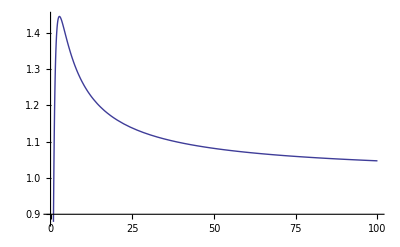

```mathematica
Plot[x^(1/x),{x,0,100}]
```

9.2-44

```mathematica
Limit[(1^x+2^x)^(1/x),x->-Infinity]
```

1

9.2-48

```mathematica
∫_0^1 n^2 x ⅇ^(-n x)ⅆx
```

1-ⅇ^-n (1+n)

9.4-55

```mathematica
Integrate[1-2/(1+y^2),{y,0,∞}]
```

Integrate::idiv: Integral of 1 - 2/1 + y^2 does not converge on {0, ∞}.

∫_0^∞ (1-2/(1+y^2))ⅆy

```mathematica
Integrate[√((1+x)/(1-x)),{x,-1,1}]
```

π

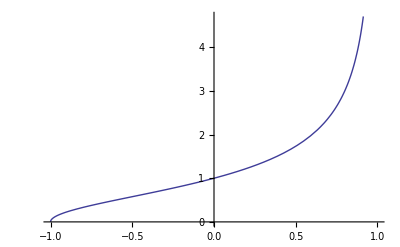

```mathematica
Plot[√((1+x)/(1-x)),{x,-1,1}]
```

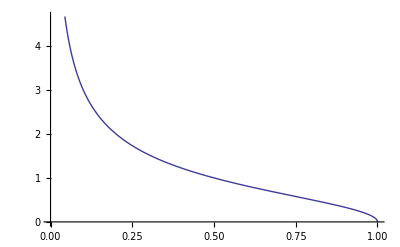

```mathematica
Plot[√((1-x)/x),{x,0,1}]
```

```mathematica
Integrate[√((1-x)/x),{x,0,1}]
```

π/2

9.4-56

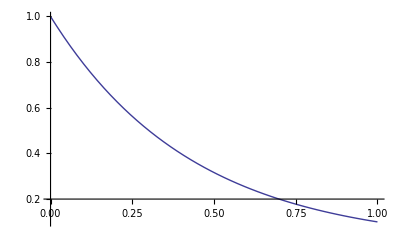

```mathematica
Plot[0.1^x,{x,0,1}]
```

10.1-36

```mathematica
RecurrenceTable[{a[n+1]==1/2(a[n]+2/a[n]),a[1]==2},a,{n,1,4}]//N
```

{2.,1.5,1.41667,1.41422}

10.1-42

```mathematica
RecurrenceTable[{a[n+1]==1.1^a[n],a[1]==0},a,{n,1,10}]//N
```

{0.,1.,1.1,1.11053,1.11165,1.11177,1.11178,1.11178,1.11178,1.11178}

```mathematica
1.1^2
```

1.21

10.5-42

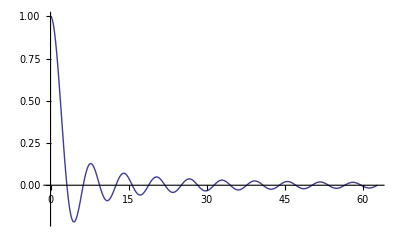

```mathematica
Plot[Sin[x]/x,{x,0,20Pi},PlotRange->All]
```

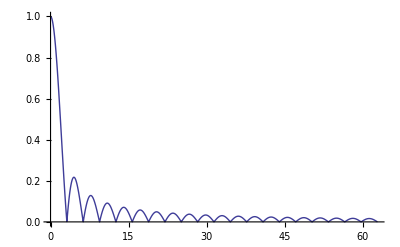

```mathematica
Plot[Abs[Sin[x]]/x,{x,0,20Pi},PlotRange->All]
```

10.5-44

```mathematica
(Sin[π/x]+x Cos[π/x]π(-1/x^2))^2+1//Expand
```

1+(π^2 Cos[π/x]^2)/x^2-(2 π Cos[π/x] Sin[π/x])/x+Sin[π/x]^2

10.7-27

```mathematica
D[x/(1-x),x]x//Simplify
```

x/(-1+x)^2

Tech10.2

```mathematica
Series[Sin[x]/x,{x,0,6}]
```

1-x^2/6+x^4/120-x^6/5040+O[x]^7

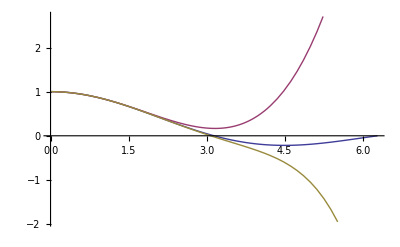

```mathematica
Needs["PlotLegends`"]
Plot[{Sin[x]/x,1-x^2/6+x^4/120,1-x^2/6+x^4/120-x^6/5040},{x,0,2Pi},PlotLegend->{"Sin[x]/x", "1-x^2/6+x^4/120", "1-x^2/6+x^4/120-x^6/5040"},LegendTextSpace->3]
```

```mathematica
Series[Tan[Sin[x]],{x,0,6}]
```

x+x^3/6-x^5/40+O[x]^7

```mathematica
Expand[∏_(i=1)^10 (1-(x/(i π))^2)]
```

11.1-21

```mathematica
Apart[2/(r/12(2-r/12))]
```

-12/(-24+r)+12/r

```mathematica
Log[2]/12 12//N
Log[2]/12 1/2//N
```

0.693147

0.0288811

```mathematica
Log[2]//N
```

0.693147

11.2-11

```mathematica
D[√Cos[x],{x,2}]
```

-1/2 √Cos[x]-Sin[x]^2/(4 Cos[x]^(3/2))

11.2-12

```mathematica
D[Cos[√x],{x,2}]
```

-Cos[√x]/(4 x)+Sin[√x]/(4 x^(3/2))

11.2-15

```mathematica
∫_(m-h)^(m+h) (a x^2+b x+c)ⅆx//Simplify
```

2/3 h (3 c+3 b m+a (h^2+3 m^2))

11.2-6

```mathematica
h/3((m-h)^3+4 m^3+(m+h)^3)//Simplify
```

2 h m (h^2+m^2)

```mathematica
∫_(m-h)^(m+h) x^3 ⅆx//Simplify
```

2 h m (h^2+m^2)

11.2-33

```mathematica
D[Sin[x]/x,x]
```

Cos[x]/x-Sin[x]/x^2

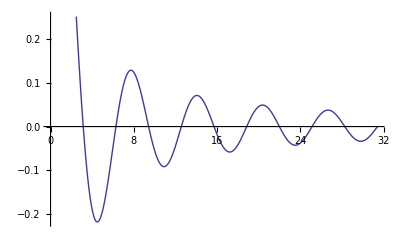

```mathematica
Plot[Sin[x]/x,{x,0,10Pi}]
```

11.2-34

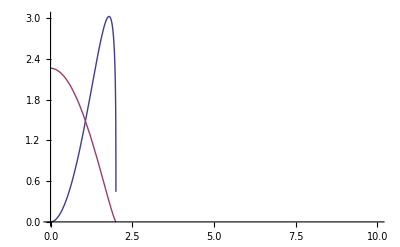

```mathematica
Plot[{x^2(4-x^2)^(1/4),2/5(4-x^2)^(5/4)},{x,0,10}]
```

11.3-21

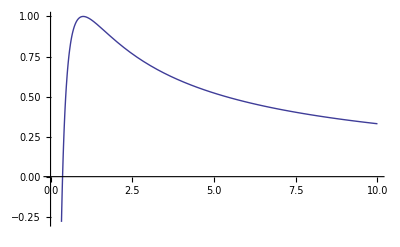

```mathematica
Plot[(1+Log[x])/x,{x,0,10}]
```

```mathematica
D[(1+Log[x])/x,x]
```

1/x^2-(1+Log[x])/x^2

```mathematica
D[(1+Log[x])/x,{x,2}]
```

-3/x^3+(2 (1+Log[x]))/x^3

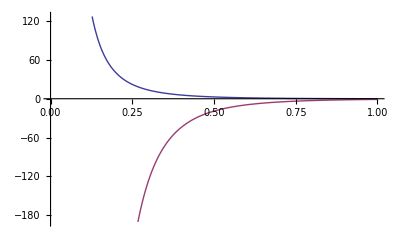

```mathematica
Plot[{1/x^2-(1+Log[x])/x^2,-3/x^3+(2 (1+Log[x]))/x^3},{x,0,1}]
```

11.3-22

```mathematica
(-5)^(1/3)//N
```

0.854988+1.48088 ⅈ

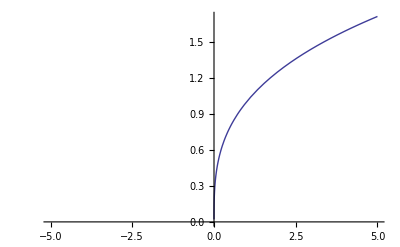

```mathematica
Plot[x^(1/3),{x,-5,5}]
```

11.3-25

```mathematica
f[1]=1
f[n_]:=2f[n-1]-1.5 f[n-1]^2
Table[f[i],{i,10}]
```

1

{1,0.5,0.625,0.664063,0.666656,0.666667,0.666667,0.666667,0.666667,0.666667}

```mathematica
1/1.5//N
```

0.666667

```mathematica
f[1]=1.2
f[n_]:=2f[n-1]-1.5 f[n-1]^2
Table[f[i],{i,10}]
```

1.2

{1.2,0.24,0.3936,0.554819,0.647902,0.666138,0.666666,0.666667,0.666667,0.666667}

```mathematica
f[1]=1
f[n_]:=2f[n-1]-1.1 f[n-1]^2
Table[f[i],{i,10}]
```

1

{1,0.9,0.909,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091}

```mathematica
1/1.1//N
```

0.909091

11.5-23

```mathematica
x[0]=0
y[0]=1
h=0.1
x[n_]:=x[n-1]+h
f[x_,y_]:=y
y1[n_]:=y[n-1]+f[x[n-1],y[n-1]]*h
y[n_]:=y[n-1]+(f[x[n-1],y[n-1]]+f[x[n],y1[n]])*h/2
ⅇ-y[10]//N
```

0

1

0.1

0.00420098

```mathematica
x[0]=0
y[0]=1
h=0.005
x[n_]:=x[n]=x[n-1]+h
f[x_,y_]:=f[x,y]=y
y1[n_]:=y1[n]=y[n-1]+f[x[n-1],y[n-1]]*h
y[n_]:=y[n]=y[n-1]+(f[x[n-1],y[n-1]]+f[x[n],y1[n]])*h/2
ⅇ-y[200]//N
```

0

1

0.005

0.0000112838

Tech11.1

```mathematica
Series[1/(1-x),{x,0,10}]
```

1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+O[x]^11

```mathematica
Series[ArcTan[x],{x,0,10}]
```

x-x^3/3+x^5/5-x^7/7+x^9/9+O[x]^11

```mathematica
Series[1/(1-x)+ArcTan[x],{x,0,10}]
```

1+2 x+x^2+(2 x^3)/3+x^4+(6 x^5)/5+x^6+(6 x^7)/7+x^8+(10 x^9)/9+x^10+O[x]^11

```mathematica
Series[Sin[Tan[x]],{x,0,10}]
Series[Tan[Sin[x]],{x,0,10}]
```

x+x^3/6-x^5/40-(55 x^7)/1008-(143 x^9)/3456+O[x]^11

x+x^3/6-x^5/40-(107 x^7)/5040-(73 x^9)/24192+O[x]^11

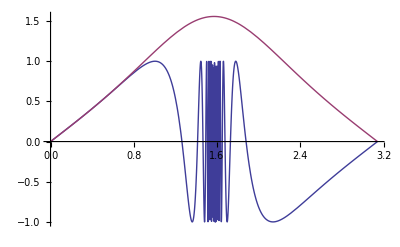

```mathematica
Plot[{Sin[Tan[x]],Tan[Sin[x]]},{x,0,Pi}]
```

Tech11.2

```mathematica
Table[1/n∑_(i=0)^(n-1) Sin[1+i/n]/(1+i/n)-0.6593299064355120,{n,{4,8,16,32,64,128,256,512,1024}}]
```

{0.0476533,0.0240016,0.0120445,0.00603317,0.00301932,0.00151034,0.000755342,0.000377713,0.000188867}

```mathematica
Table[1/n∑_(i=1)^n Sin[1+i/n]/(1+i/n)-0.6593299064355120,{n,{4,8,16,32,64,128,256,512,1024}}]
```

{-0.0490522,-0.0243512,-0.0121319,-0.00605502,-0.00302478,-0.00151171,-0.000755683,-0.000377799,-0.000188889}

```mathematica
Table[1/n∑_(i=1)^n Sin[1+i/n-1/2 1/n]/(1+i/n-1/2 1/n)-0.6593299064355120,{n,{4,8,16,32,64,128,256,512,1024}}]
```

{0.000349839,0.0000874065,0.0000218483,5.46187×10^-6,1.36545×10^-6,3.41363×10^-7,8.53406×10^-8,2.13351×10^-8,5.33378×10^-9}

```mathematica
Table[1/(2n)(Sin[1]/1+2(∑_(i=1)^(n-1) Sin[1+i/n]/(1+i/n))+Sin[2]/2)-0.6593299064355120,{n,{4,8,16,32,64,128,256,512,1024}}]
```

{-0.000699435,-0.000174798,-0.0000436956,-0.0000109237,-2.7309×10^-6,-6.82725×10^-7,-1.70681×10^-7,-4.26703×10^-8,-1.06676×10^-8}

```mathematica
Table[1/(3n)(Sin[1]/1+2(∑_(i=1)^(n/2-1) Sin[1+(2i)/n]/(1+(2i)/n))+4(∑_(i=1)^(n/2) Sin[1+(2i-1)/n]/(1+(2i-1)/n))+Sin[2]/2)-0.6593299064355120,{n,{4,8,16,32,64,128,256,512,1024}}]
```

{1.30451×10^-6,8.12665×10^-8,5.07503×10^-9,3.17125×10^-10,1.98189×10^-11,1.23845×10^-12,7.70495×10^-14,4.66294×10^-15,0.}

Tech11.3

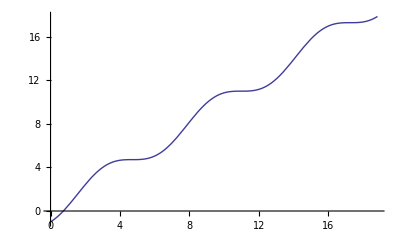

```mathematica
Plot[x-Cos[x],{x,0,6Pi}]
```

```mathematica
a=0 
b=1
m=(a+b)/2
f[x_]:=x-Cos[x]
While[f[m]≠0&&(b-a)/2>=0.01,If[f[a]*f[m]<0,b=m,a=m];m=(a+b)/2]
m//N
```

0

1

1/2

0.742188

```mathematica
FindRoot[z-Cos[z]==0,{z,0}]
```

{z→0.739085}

```mathematica
x=0
y=1
f[x_]:=Cos[x]
While[Abs[x-y]>=0.01,y=x;x=f[x]]
x//N
```

0

1

0.735605

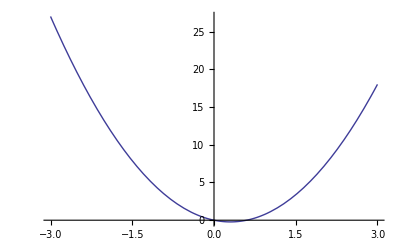

```mathematica
Plot[x-2.5x(1-x),{x,-3,3}]
```

```mathematica
x=0.1
y=1
f[x_]:=2.5x(1-x)
While[Abs[x-y]>=0.0001,y=x;x=f[x]]
x//N
```

0.1

1

0.59997

```mathematica
Solve[z-2.5z(1-z)==0,z]
```

{{z→0.},{z→0.6}}

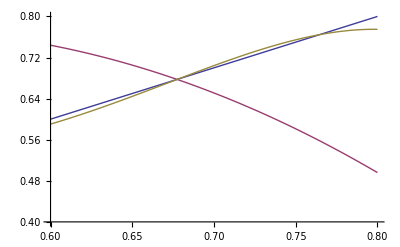

```mathematica
Plot[{x,3.1x(1-x),9.61 x-39.401 x^2+59.582 x^3-29.791 x^4},{x,0.6,0.8},PlotRange->{0.4,0.8}]
```

```mathematica
x=0.1
y=1
n=1
f[x_]:=3.1x(1-x)
While[n<20,Print[x];y=x;x=f[x];n++]
```

0.1

1

1

0.1

0.279

0.623593

0.727647

0.614348

0.734466

0.60458

0.741095

0.594806

0.747136

0.585663

0.752252

0.577744

0.756263

0.571421

0.759187

0.566748

0.761189

0.56352

```mathematica
Solve[z-3.1z(1-z)==0,z]
```

{{z→0.},{z→0.677419}}

```mathematica
f[x_]:=3.1x(1-x)
f[f[x]]//Expand
```

9.61 x-39.401 x^2+59.582 x^3-29.791 x^4

12.1-42

```mathematica
((a^2+b^2)(b-a))/2-1/2 1/2(b-a)(a^2+b^2+2((b+a)/2)^2)//Simplify
```

-1/8 (a-b)^3

```mathematica
-1/8 (a-b)^3*4/3
```

```mathematica
((a^2+b^2)(b-a))/2-(-1/6 (a-b)^3)//Simplify
```

1/3 (-a^3+b^3)

```mathematica
Solve[{y==k(x-p),y^2==4p x},{x,y}]
```

{{x→(p^2+(2 p^2)/k^2-(2 p √((1+k^2) p^2))/k^2)/p,y→(2 (p-√(p^2+k^2 p^2)))/k},{x→(p^2+(2 p^2)/k^2+(2 p √((1+k^2) p^2))/k^2)/p,y→(2 (p+√(p^2+k^2 p^2)))/k}}

12.5-1

```mathematica
x=u Cos[θ]-v Sin[θ]/.{Sin[θ]-> √(1/2),Cos[θ]-> √(1/2)}
y=u Sin[θ]+v Cos[θ]/.{Sin[θ]-> √(1/2),Cos[θ]-> √(1/2)}
```

u/(√2)-v/(√2)

u/(√2)+v/(√2)

```mathematica
x^2+x y+y^2==6/.{x->u/(√2)-v/(√2),y->u/(√2)+v/(√2)}//Simplify
```

3 u^2+v^2==12

12.5-13

```mathematica
x Cos[θ]+y Sin[θ]==d/.{x->u Cos[θ]-v Sin[θ],y->u Sin[θ]+v Cos[θ]}//Simplify
```

d==u

12.5-14

```mathematica
x^(1/2)+y^(1/2)==a^(1/2)/.{x->u/(√2)-v/(√2),y->u/(√2)+v/(√2)}
```

√(u/(√2)-v/(√2))+√(u/(√2)+v/(√2))==√a

```mathematica
(√(u/(√2)-v/(√2))+√(u/(√2)+v/(√2)))^2==a//Simplify
```

√2 (u+√(u-v) √(u+v))==a

```mathematica
(√(u-v) √(u+v))^2==(a/(√2)-u)^2//Simplify
```

a^2+2 v^2==2 √2 a u

12.5-15

```mathematica
Solve[{x==u Cos[θ]-v Sin[θ],y==u Sin[θ]+v Cos[θ]},{u,v}]
```

{{u→-(-x Cos[θ]-y Sin[θ])/(Cos[θ]^2+Sin[θ]^2),v→-(-y Cos[θ]+x Sin[θ])/(Cos[θ]^2+Sin[θ]^2)}}

12.5-16

```mathematica
√((1+(-24/25))/2)
√((1-(-24/25))/2)
```

1/(5 √2)

7/(5 √2)

```mathematica
{x=u Cos[θ]-v Sin[θ],y=u Sin[θ]+v Cos[θ]}/.{Sin[θ]-> 1/(5 √2),Cos[θ]-> 7/(5 √2)}
```

{(7 u)/(5 √2)-v/(5 √2),u/(5 √2)+(7 v)/(5 √2)}

```mathematica
x^2+14x y+49 y^2==100/.{x->(7 u)/(5 √2)-v/(5 √2),y->u/(5 √2)+(7 v)/(5 √2)}//Simplify
```

2/25 (7 u+24 v)^2==100

12.5-18

```mathematica
x=u Cos[θ]-v Sin[θ]
y=u Sin[θ]+v Cos[θ]
Collect[A x^2+B x y+C y^2+D x+E y+F,{u,v},Simplify]
```

u Cos[θ]-v Sin[θ]

v Cos[θ]+u Sin[θ]

F+v (ⅇ Cos[θ]-D Sin[θ])+v^2 (C Cos[θ]^2-B Cos[θ] Sin[θ]+A Sin[θ]^2)+u^2 (A Cos[θ]^2+B Cos[θ] Sin[θ]+C Sin[θ]^2)+u (D Cos[θ]+ⅇ Sin[θ]+v (B Cos[2 θ]+(-A+C) Sin[2 θ]))

```mathematica
(C Cos[θ]^2-B Cos[θ] Sin[θ]+A Sin[θ]^2)+(A Cos[θ]^2+B Cos[θ] Sin[θ]+C Sin[θ]^2)//Simplify
```

A+C

```mathematica
(B Cos[2 θ]+(-A+C) Sin[2 θ])^2-4 (C Cos[θ]^2-B Cos[θ] Sin[θ]+A Sin[θ]^2)(A Cos[θ]^2+B Cos[θ] Sin[θ]+C Sin[θ]^2)//Simplify
```

B^2-4 A C

```mathematica
(B Cos[2 θ]+(-A+C) Sin[2 θ])^2-4 (C Cos[θ]^2-B Cos[θ] Sin[θ]+A Sin[θ]^2)(A Cos[θ]^2+B Cos[θ] Sin[θ]+C Sin[θ]^2)//Expand
Collect[%,{A,B,C}]
```

-4 A C Cos[θ]^4+B^2 Cos[2 θ]^2+4 A B Cos[θ]^3 Sin[θ]-4 B C Cos[θ]^3 Sin[θ]-4 A^2 Cos[θ]^2 Sin[θ]^2+4 B^2 Cos[θ]^2 Sin[θ]^2-4 C^2 Cos[θ]^2 Sin[θ]^2-4 A B Cos[θ] Sin[θ]^3+4 B C Cos[θ] Sin[θ]^3-4 A C Sin[θ]^4-2 A B Cos[2 θ] Sin[2 θ]+2 B C Cos[2 θ] Sin[2 θ]+A^2 Sin[2 θ]^2-2 A C Sin[2 θ]^2+C^2 Sin[2 θ]^2

B^2 (Cos[2 θ]^2+4 Cos[θ]^2 Sin[θ]^2)+B C (-4 Cos[θ]^3 Sin[θ]+4 Cos[θ] Sin[θ]^3+2 Cos[2 θ] Sin[2 θ])+A^2 (-4 Cos[θ]^2 Sin[θ]^2+Sin[2 θ]^2)+C^2 (-4 Cos[θ]^2 Sin[θ]^2+Sin[2 θ]^2)+A (B (4 Cos[θ]^3 Sin[θ]-4 Cos[θ] Sin[θ]^3-2 Cos[2 θ] Sin[2 θ])+C (-4 Cos[θ]^4-4 Sin[θ]^4-2 Sin[2 θ]^2))

```mathematica
TrigExpand[(2 Cos[2 θ] Sin[2 θ])]
```

4 Cos[θ]^3 Sin[θ]-4 Cos[θ] Sin[θ]^3

12.5-23

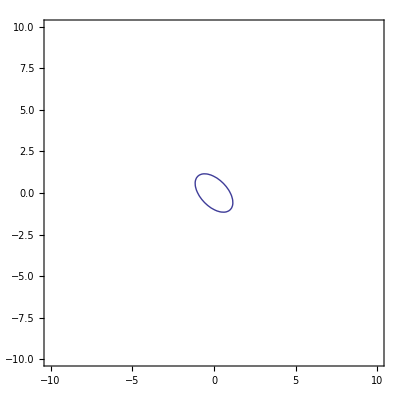

```mathematica
ContourPlot[x^2+1x y+y^2==1,{x,-10,10},{y,-10,10}]
```

12.6-44

```mathematica
(1/(1+Cos[π/2-Subscript[θ, 0]]))/(1/(1+Cos[π/4-Subscript[θ, 0]]))==4/3
```

```mathematica
(1+TrigExpand[Cos[π/4-Subscript[θ, 0]]])/(1+Sin[Subscript[θ, 0]])==4/3//Simplify
```

(2+√2 Cos[θ_0]+√2 Sin[θ_0])/(2+2 Sin[θ_0])==4/3

```mathematica
3(2+√2 Cos[Subscript[θ, 0]]+√2 Sin[Subscript[θ, 0]])-4(2+2 Sin[Subscript[θ, 0]])==0//Simplify//N
```

4.24264 Cos[θ_0]-3.75736 Sin[θ_0]==2.

12.6-45

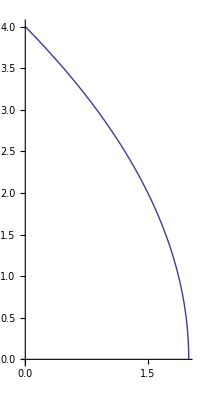

```mathematica
PolarPlot[4/(1+Cos[t]),{t,0,π/2}]
```

12.7-18

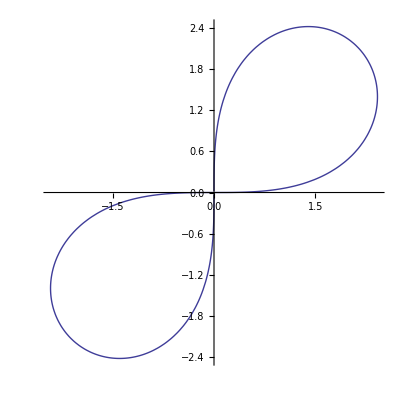

```mathematica
PolarPlot[√(9Sin[2t]),{t,0,2π}]
```

12-7.23

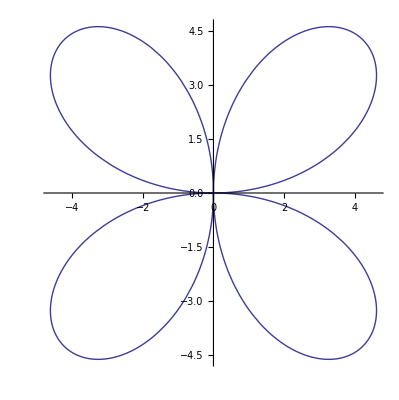

```mathematica
PolarPlot[6Sin[2t],{t,0,2π}]
```

12.7-24

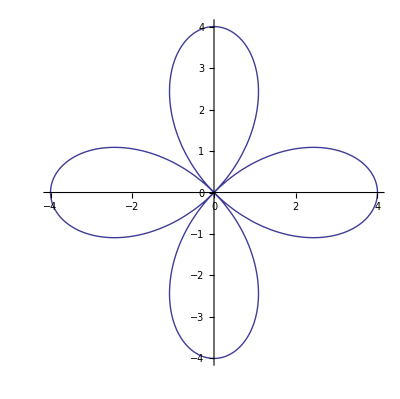

```mathematica
PolarPlot[4Cos[2t],{t,0,2π}]
```

12.7-25

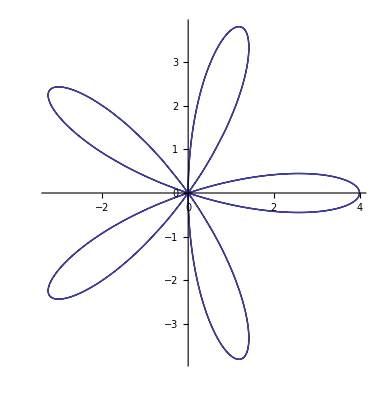

```mathematica
PolarPlot[4Cos[5t],{t,0,2π}]
```

12.7-26

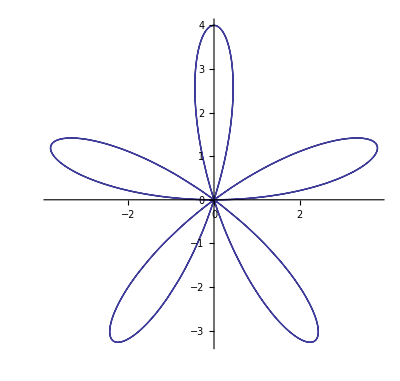

```mathematica
PolarPlot[4Sin[5t],{t,0,2π}]
```

12.7-34

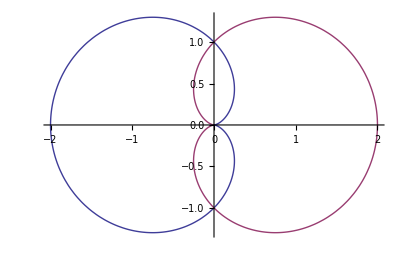

```mathematica
PolarPlot[{1-Cos[t],1+Cos[t]},{t,0,2π}]
```

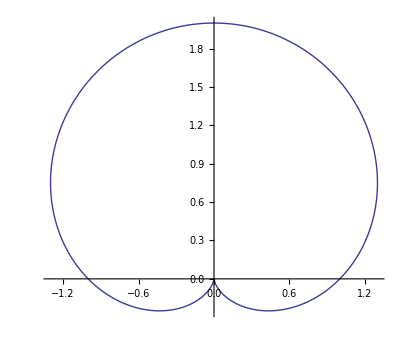

```mathematica
PolarPlot[1+Sin[t],{t,0,2π}]
```

12.7-35

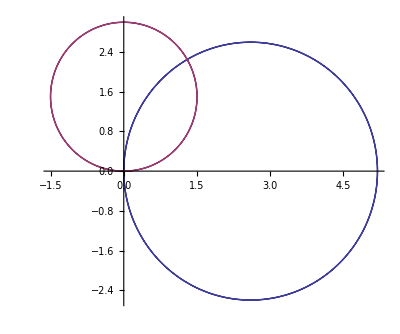

```mathematica
PolarPlot[{3 √3 Cos[t],3Sin[t]},{t,0,2π}]
```

12.7-37

```mathematica
Solve[x+2 x^2==1,x]
```

{{x→-1},{x→1/2}}

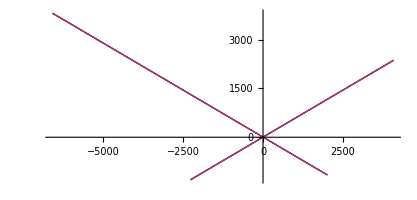

```mathematica
PolarPlot[{6Sin[t],6/(1+2Sin[t])},{t,0,2π}]
```

12.7-40

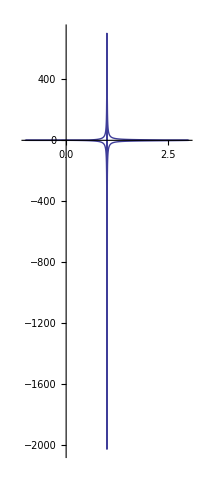

```mathematica
PolarPlot[1/Cos[t]+2,{t,0,2π}]
```

12.7-44

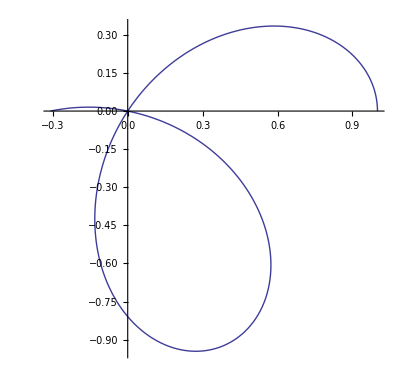

```mathematica
PolarPlot[Cos[(8t)/5],{t,0,π}]
```

12.7-45

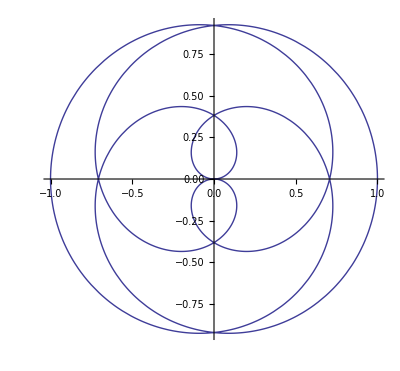

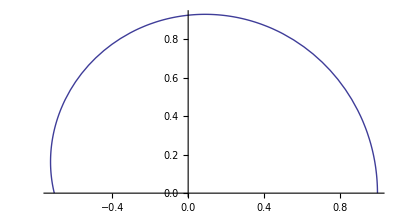

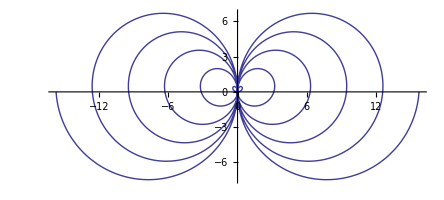

```mathematica
PolarPlot[Cos[t/4],{t,0,8π}]
PolarPlot[Cos[t/4],{t,0,π}]
PolarPlot[t Cos[t],{t,-5π,5π}]
```

12.7-50

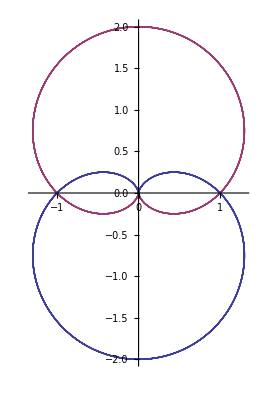

```mathematica
PolarPlot[{1-Sin[t],1+Sin[t]},{t,0,8π}]
```

12.7-51

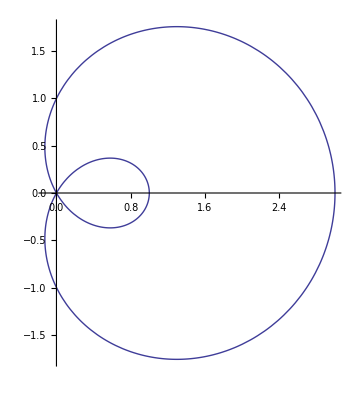

```mathematica
PolarPlot[{1+2Cos[t]},{t,0,2π}]
```

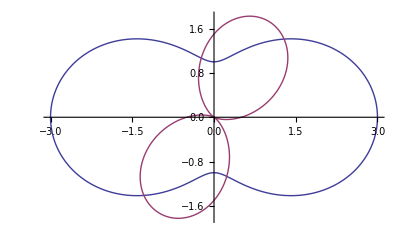

```mathematica
PolarPlot[{2+1Cos[2t],1+1Cos[2(t-π/3)]},{t,0,2π}]
```

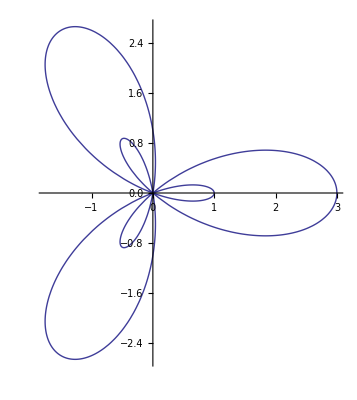

```mathematica
PolarPlot[{1+2Cos[3t]},{t,0,2π}]
```

12.7-52

```mathematica
Manipulate[PolarPlot[Abs[Cos[n t]],{t,0,2π}],{n,0,10,1}]
```

12.7-53

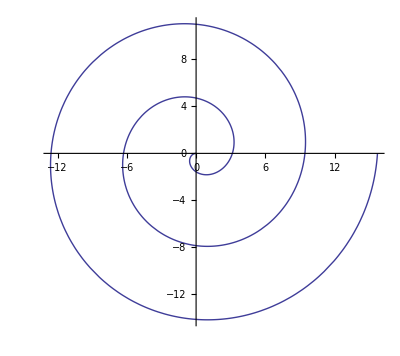

```mathematica
PolarPlot[{- t},{t,0,5π}]
```

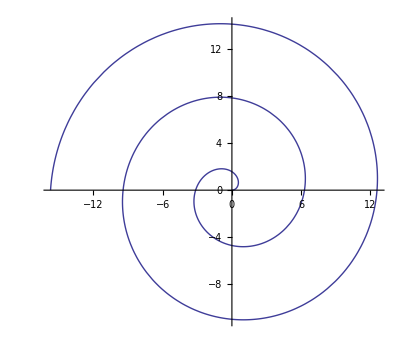

```mathematica
PolarPlot[{ t},{t,0,5π}]
```

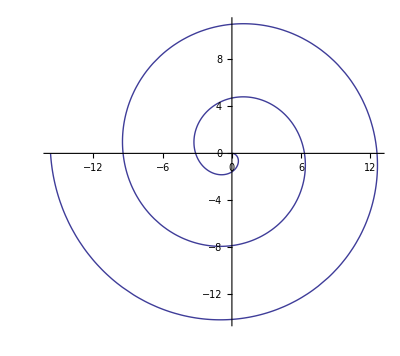

```mathematica
PolarPlot[{- t},{t,-5π,0}]
```

12.7-54

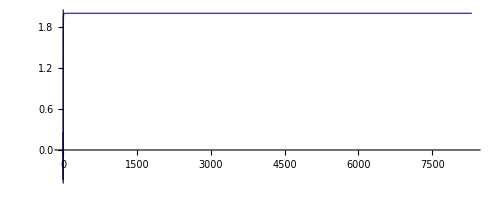

```mathematica
PolarPlot[ 2/t,{t,0,5π}]
```

12.7-55

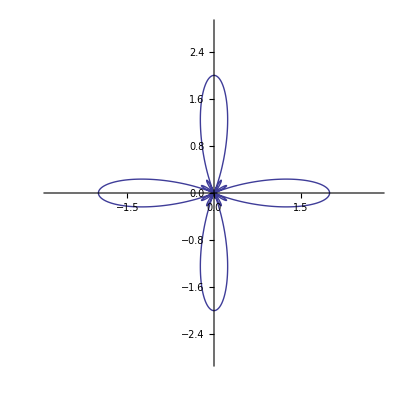

```mathematica
PolarPlot[Cos[4t]+(Cos[4t])^2,{t,0,2π},PlotRange->All]
```

12.8-15

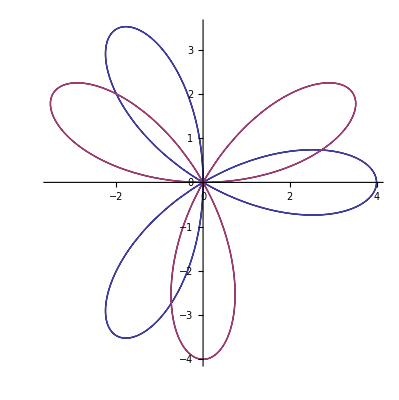

```mathematica
PolarPlot[{4Cos[3t],4Sin[3t]},{t,0,2π}]
```

12.8-20

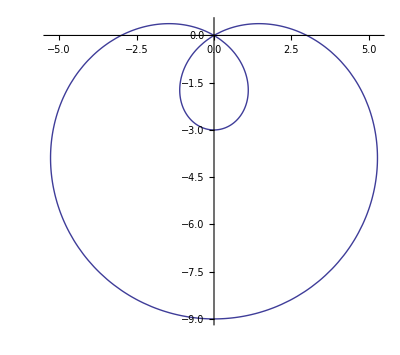

```mathematica
PolarPlot[3-6Sin[t],{t,0,2π}]
```

12.8-30

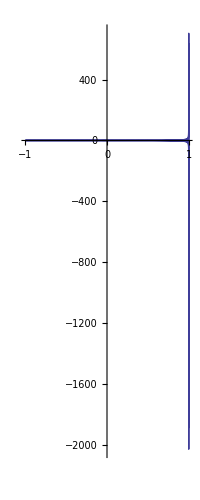

```mathematica
PolarPlot[Sec[t]-2Cos[t],{t,0,2π}]
```

12.8-31

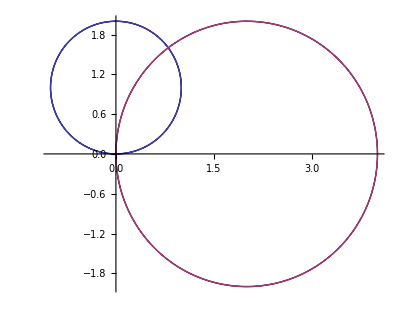

```mathematica
PolarPlot[{2Sin[t],4Cos[t]},{t,0,2π}]
```

Tech12.1

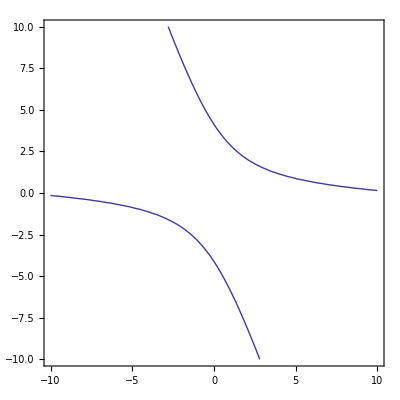

```mathematica
ContourPlot[x^2+24x y+8 y^2-136==0,{x,-10,10},{y,-10,10}]
```

```mathematica
f[x_,y_]:=x^2+24x y+8 y^2-136
f[u Cos[θ]-v Sin[θ],u Sin[θ]+v Cos[θ]]
```

-136+8 (v Cos[θ]+u Sin[θ])^2+24 (v Cos[θ]+u Sin[θ]) (u Cos[θ]-v Sin[θ])+(u Cos[θ]-v Sin[θ])^2

```mathematica
Manipulate[ContourPlot[f[u Cos[θ]-v Sin[θ],u Sin[θ]+v Cos[θ]]==0,{u,-10,10},{v,-10,10}],{θ,0,2π,π/12}]
```

Tech12.2

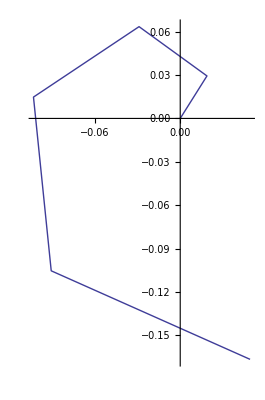

```mathematica
ListPolarPlot[Table[{n,Sin[(2n)/180 π]},{n,0,5}],Joined->True]
```

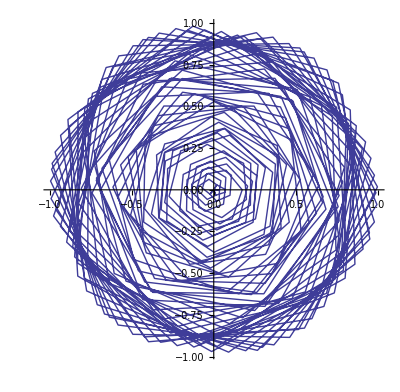

```mathematica
ListPolarPlot[Table[{n,Sin[(2n)/180 π]},{n,0,360}],Joined->True]
```

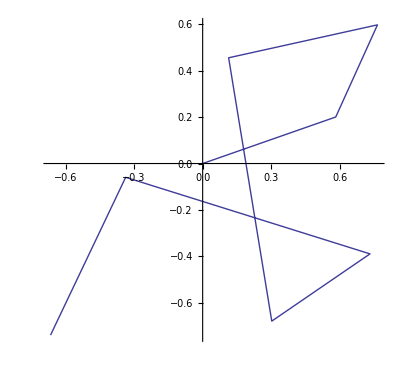

```mathematica
ListPolarPlot[Table[{19 n/180 π,Sin[2*(19n)/180 π]},{n,{0,1,2,4,6,8,10,12}}],Joined->True]
```

2

5

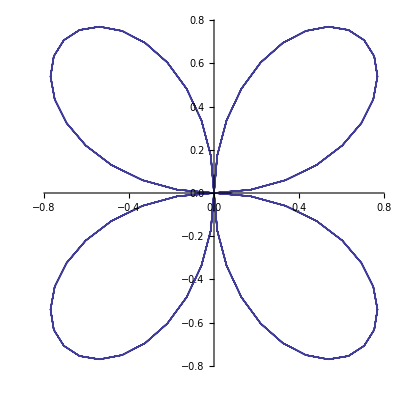

```mathematica
n=2
d=5
ListPolarPlot[Table[{k/180 π,Sin[(n k)/180 π]},{k,0,d*360,d}],Joined->True]
```

```mathematica
120
```

120

7

29

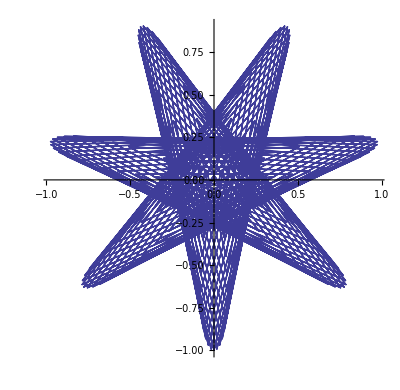

```mathematica
n=7
d=29
ListPolarPlot[Table[{k/180 π,Sin[(n k)/180 π]},{k,0,d*360,d}],Joined->True]
```

5

29

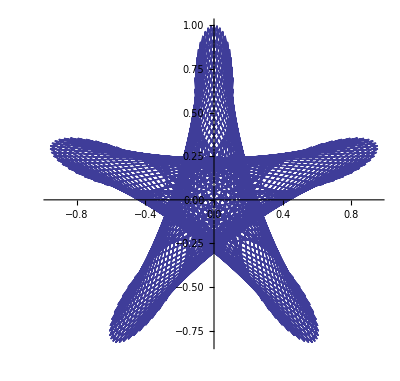

```mathematica
n=5
d=29
ListPolarPlot[Table[{k/180 π,Sin[(n k)/180 π]},{k,0,d*360,d}],Joined->True]
```

```mathematica
d=19
Table[Mod[i,360],{i,0,d*360,d}]
```

19

{0,19,38,57,76,95,114,133,152,171,190,209,228,247,266,285,304,323,342,1,20,39,58,77,96,115,134,153,172,191,210,229,248,267,286,305,324,343,2,21,40,59,78,97,116,135,154,173,192,211,230,249,268,287,306,325,344,3,22,41,60,79,98,117,136,155,174,193,212,231,250,269,288,307,326,345,4,23,42,61,80,99,118,137,156,175,194,213,232,251,270,289,308,327,346,5,24,43,62,81,100,119,138,157,176,195,214,233,252,271,290,309,328,347,6,25,44,63,82,101,120,139,158,177,196,215,234,253,272,291,310,329,348,7,26,45,64,83,102,121,140,159,178,197,216,235,254,273,292,311,330,349,8,27,46,65,84,103,122,141,160,179,198,217,236,255,274,293,312,331,350,9,28,47,66,85,104,123,142,161,180,199,218,237,256,275,294,313,332,351,10,29,48,67,86,105,124,143,162,181,200,219,238,257,276,295,314,333,352,11,30,49,68,87,106,125,144,163,182,201,220,239,258,277,296,315,334,353,12,31,50,69,88,107,126,145,164,183,202,221,240,259,278,297,316,335,354,13,32,51,70,89,108,127,146,165,184,203,222,241,260,279,298,317,336,355,14,33,52,71,90,109,128,147,166,185,204,223,242,261,280,299,318,337,356,15,34,53,72,91,110,129,148,167,186,205,224,243,262,281,300,319,338,357,16,35,54,73,92,111,130,149,168,187,206,225,244,263,282,301,320,339,358,17,36,55,74,93,112,131,150,169,188,207,226,245,264,283,302,321,340,359,18,37,56,75,94,113,132,151,170,189,208,227,246,265,284,303,322,341,0}

```mathematica
d=29
Table[Mod[i,360],{i,0,d*360,d}]
```

29

{0,29,58,87,116,145,174,203,232,261,290,319,348,17,46,75,104,133,162,191,220,249,278,307,336,5,34,63,92,121,150,179,208,237,266,295,324,353,22,51,80,109,138,167,196,225,254,283,312,341,10,39,68,97,126,155,184,213,242,271,300,329,358,27,56,85,114,143,172,201,230,259,288,317,346,15,44,73,102,131,160,189,218,247,276,305,334,3,32,61,90,119,148,177,206,235,264,293,322,351,20,49,78,107,136,165,194,223,252,281,310,339,8,37,66,95,124,153,182,211,240,269,298,327,356,25,54,83,112,141,170,199,228,257,286,315,344,13,42,71,100,129,158,187,216,245,274,303,332,1,30,59,88,117,146,175,204,233,262,291,320,349,18,47,76,105,134,163,192,221,250,279,308,337,6,35,64,93,122,151,180,209,238,267,296,325,354,23,52,81,110,139,168,197,226,255,284,313,342,11,40,69,98,127,156,185,214,243,272,301,330,359,28,57,86,115,144,173,202,231,260,289,318,347,16,45,74,103,132,161,190,219,248,277,306,335,4,33,62,91,120,149,178,207,236,265,294,323,352,21,50,79,108,137,166,195,224,253,282,311,340,9,38,67,96,125,154,183,212,241,270,299,328,357,26,55,84,113,142,171,200,229,258,287,316,345,14,43,72,101,130,159,188,217,246,275,304,333,2,31,60,89,118,147,176,205,234,263,292,321,350,19,48,77,106,135,164,193,222,251,280,309,338,7,36,65,94,123,152,181,210,239,268,297,326,355,24,53,82,111,140,169,198,227,256,285,314,343,12,41,70,99,128,157,186,215,244,273,302,331,0}

13.1-9

```mathematica
(y+4)^3+16(y+4)-8(y+4)^2//Expand
```

4 y^2+y^3

13.1-59,60

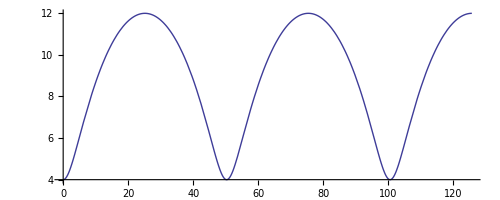

```mathematica
ParametricPlot[{8t-4Sin[t],8-4Cos[t]},{t,0,5Pi}]
```

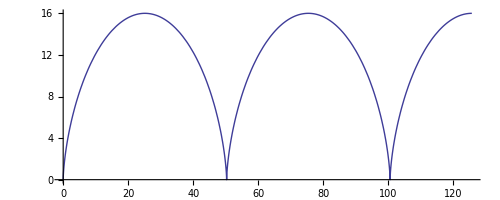

```mathematica
ParametricPlot[{8t-8Sin[t],8-8Cos[t]},{t,0,5Pi}]
```

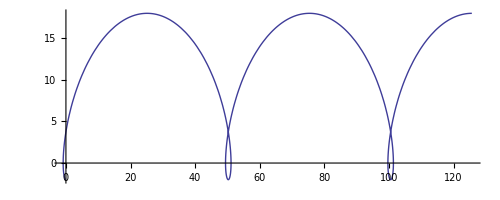

```mathematica
ParametricPlot[{8t-10Sin[t],8-10Cos[t]},{t,0,5Pi}]
```

13.1-62

```mathematica
TrigExpand[Cos[3t]]
```

Cos[t]^3-3 Cos[t] Sin[t]^2

13.1-64

```mathematica
TrigExpand[Cos[2t]]
```

Cos[t]^2-Sin[t]^2

13.1-65

```mathematica
(Sin[t]+Sin[2t])^2+(Cos[t]-Cos[2t])^2//Simplify
```

4 Sin[(3 t)/2]^2

13.1-67

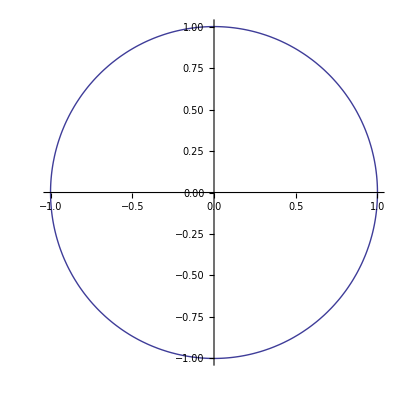

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

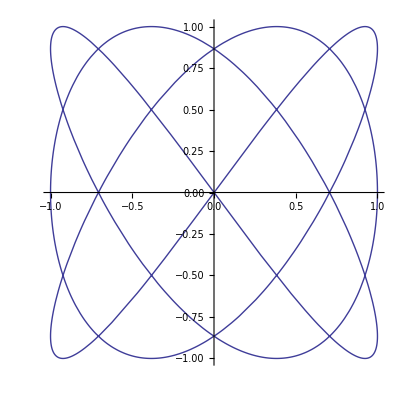

```mathematica
ParametricPlot[{Cos[3t],Sin[4t]},{t,0,2Pi}]
```

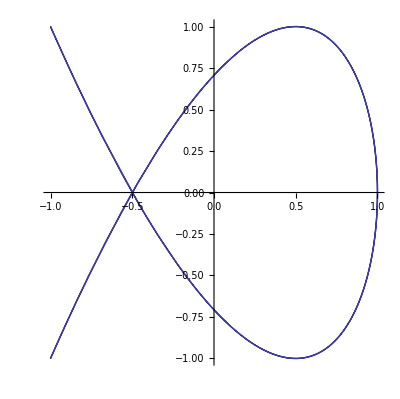

```mathematica
ParametricPlot[{Cos[2t],Sin[3t]},{t,0,2Pi}]
```

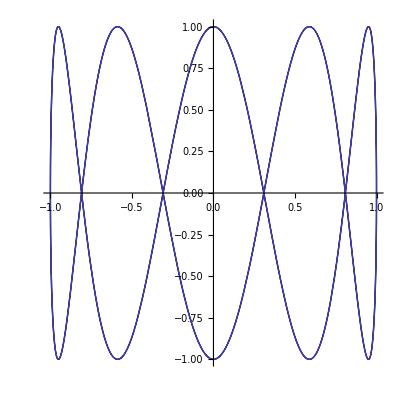

```mathematica
ParametricPlot[{Cos[2t],Sin[10t]},{t,0,2Pi}]
```

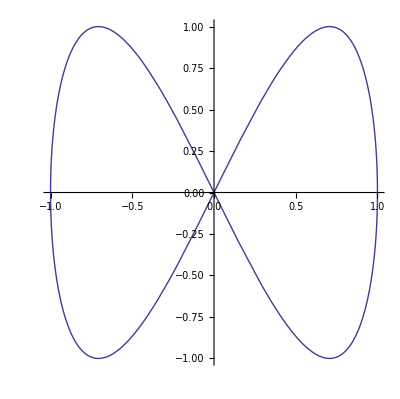

-Graphics-

```mathematica
ParametricPlot[{Cos[t],Sin[2t]},{t,0,2Pi}]
ParametricPlot[{Cos[2t],Sin[4t]},{t,0,Pi}]
```

13.1-69

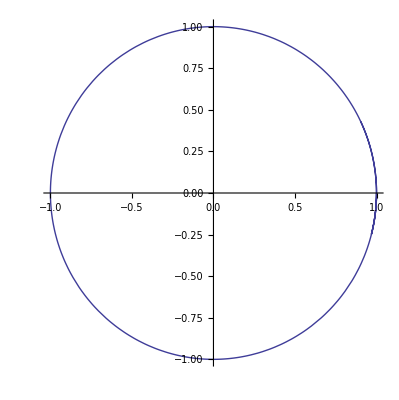

```mathematica
ParametricPlot[{Cos[t^2-t],Sin[t^2-t]},{t,0,π}]
```

13.1-70

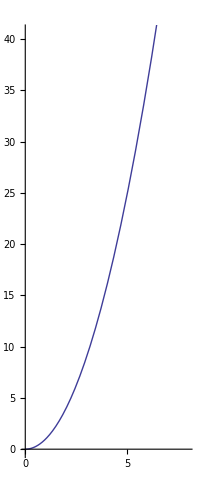

```mathematica
ParametricPlot[{t^3,t^6},{t,0,2}]
```

13.1-71

4

1

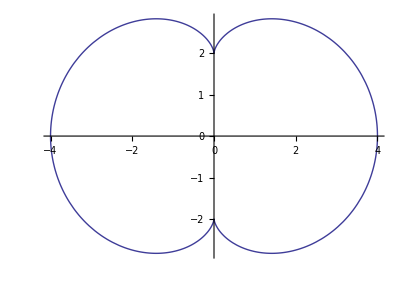

```mathematica
a=4
b=1
ParametricPlot[{(a-b)Cos[t]+b Cos[(a-b)/b t],(a-b)Sin[t]+b Sin[(a-b)/b t]},{t,0,2π}]
```

7

2

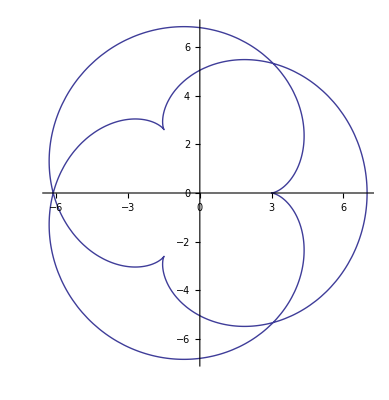

```mathematica
a=7
b=2
ParametricPlot[{(a-b)Cos[t]+b Cos[(a-b)/b t],(a-b)Sin[t]+b Sin[(a-b)/b t]},{t,0,4π}]
```

13.1-73

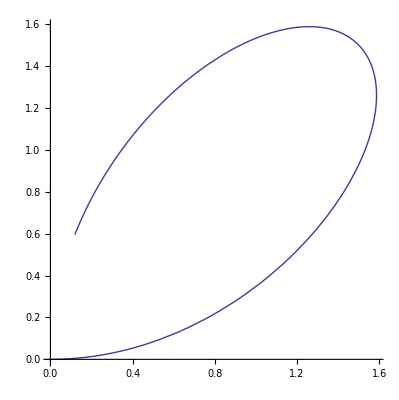

```mathematica
ParametricPlot[{(3t)/(t^3+1),(3 t^2)/(t^3+1)},{t,0,5}]
```

13.5-57

```mathematica
D[r[θ]Cos[θ],θ]
```

-r[θ] Sin[θ]+Cos[θ] r'[θ]

```mathematica
D[r[θ]Sin[θ],θ]
```

Cos[θ] r[θ]+Sin[θ] r'[θ]

```mathematica
D[r[θ]Cos[θ],{θ,2}]
```

-Cos[θ] r[θ]-2 Sin[θ] r'[θ]+Cos[θ] r''[θ]

```mathematica
D[r[θ]Sin[θ],{θ,2}]
```

-r[θ] Sin[θ]+2 Cos[θ] r'[θ]+Sin[θ] r''[θ]

```mathematica
D[r[θ]Cos[θ],θ]D[r[θ]Sin[θ],{θ,2}]-D[r[θ]Sin[θ],θ]D[r[θ]Cos[θ],{θ,2}]//Simplify
```

r[θ]^2+2 r'[θ]^2-r[θ] r''[θ]

13.5-66

```mathematica
D[{x[t], y[t]},t]
```

{x'[t],y'[t]}

```mathematica
D[{x'[t],y'[t]}/(√((x'[t])^2+(y'[t])^2)),t]//Simplify
```

{(y'[t] (y'[t] x''[t]-x'[t] y''[t]))/((x'[t]^2+y'[t]^2)^(3/2)),(x'[t] (-y'[t] x''[t]+x'[t] y''[t]))/((x'[t]^2+y'[t]^2)^(3/2))}

```mathematica
((y'[t] (y'[t] x''[t]-x'[t] y''[t]))/((x'[t]^2+y'[t]^2)^(3/2)))^2+((x'[t] (-y'[t] x''[t]+x'[t] y''[t]))/((x'[t]^2+y'[t]^2)^(3/2)))^2//Simplify
```

(y'[t] x''[t]-x'[t] y''[t])^2/((x'[t]^2+y'[t]^2)^2)

13.5-68

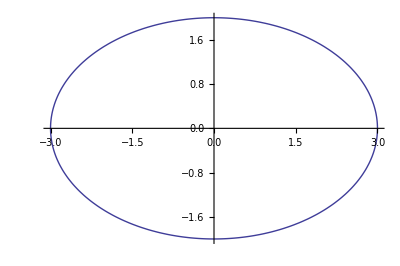
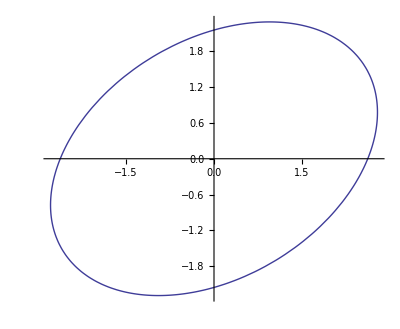
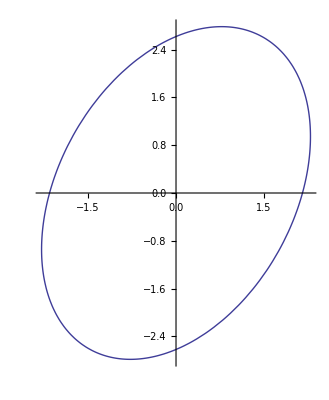
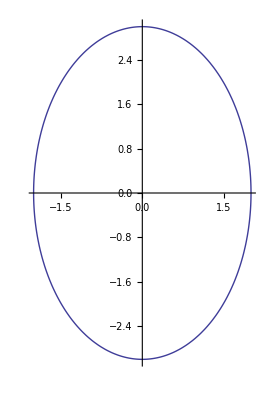
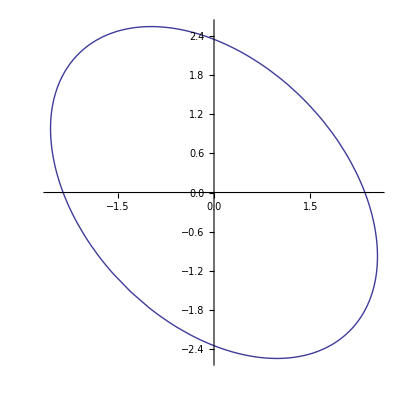

```mathematica
Table[ParametricPlot[{2.5Cos[t]+0.5Cos[t-2θ],2.5Sin[t]-0.5Sin[t-2θ]},{t,0,2Pi}],{θ,{0,π/6,π/3,π/2,(3π)/4}}]
```

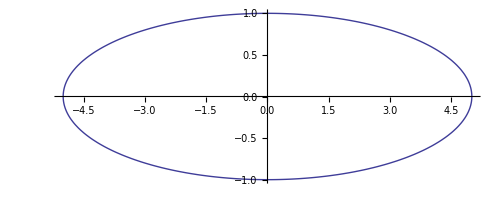
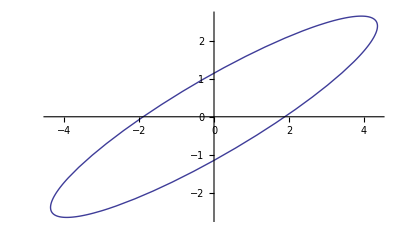
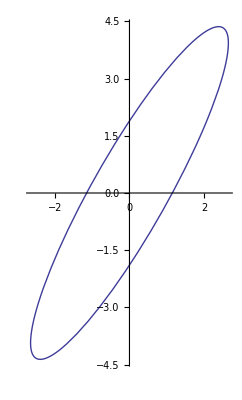
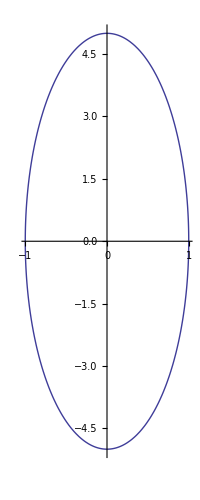
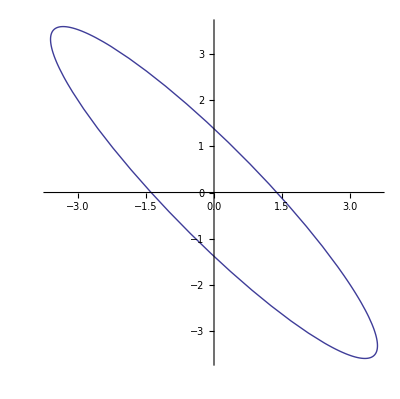

```mathematica
Table[ParametricPlot[{3Cos[t]+2Cos[t-2θ],3Sin[t]-2Sin[t-2θ]},{t,0,2Pi}],{θ,{0,π/6,π/3,π/2,(3π)/4}}]
```

Tech13.1

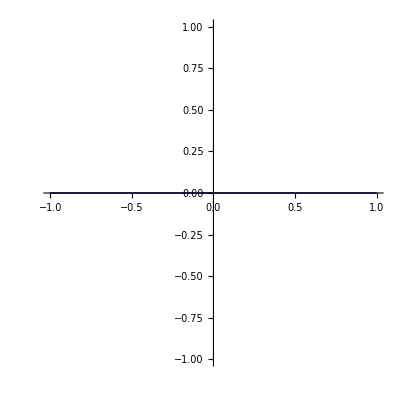
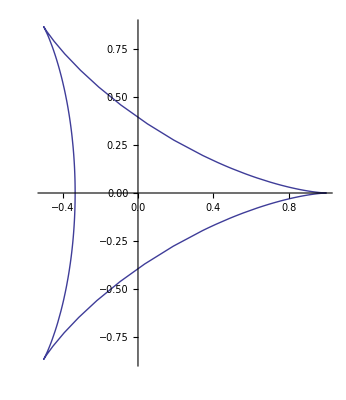
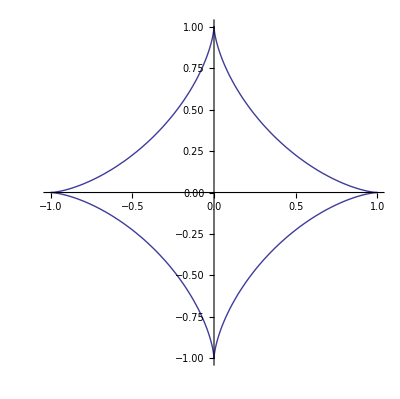
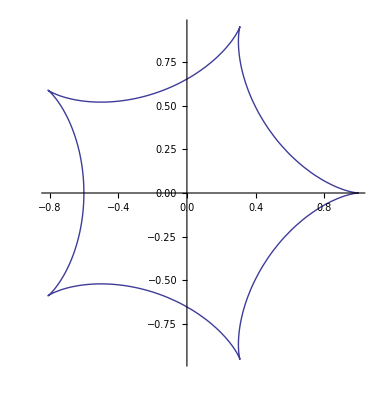

```mathematica
Table[ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,2Pi}],{a,{1}},{b,{1/2,1/3,1/4,1/5}}]
```

```mathematica
(a-b)^2 (Sin[u]+Sin[((a-b) u)/b])^2+(a-b)^2 (Cos[u]-Cos[((a-b) u)/b])^2//Simplify
```

4 (a-b)^2 Sin[(a u)/(2 b)]^2

```mathematica
Table[∫_0^(2Pi) √((D[(a-b)Cos[u]+b Cos[(a-b)/b u],u])^2+(D[(a-b)Sin[u]-b Sin[(a-b)/b u],u])^2)ⅆu,{a,{1}},{b,{1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}}]
```

{{16/3,6,32/5,20/3,48/7,7,64/9,36/5}}

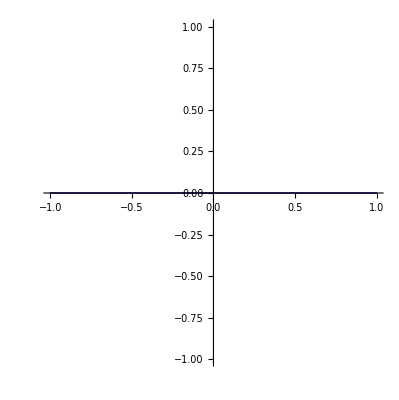

```mathematica
ParametricPlot[{1/2 Cos[u]+1/2 Cos[u],1/2 Sin[u]-1/2 Sin[u]},{u,0,4Pi}]
```

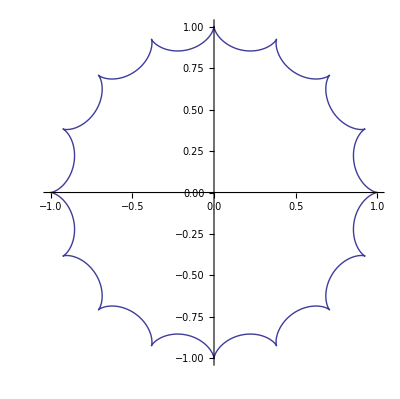
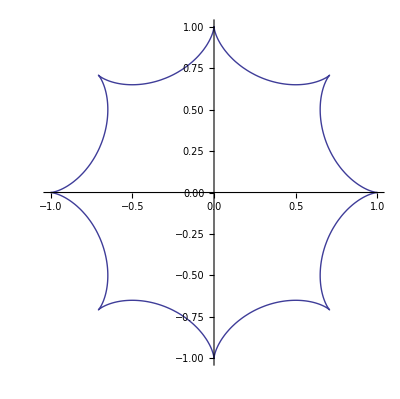
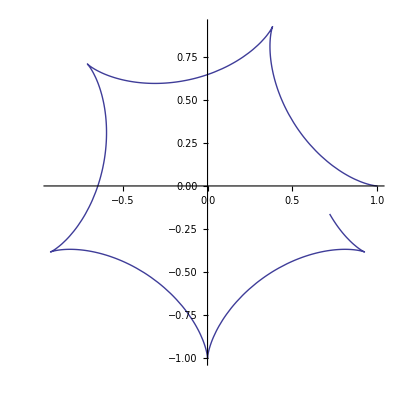
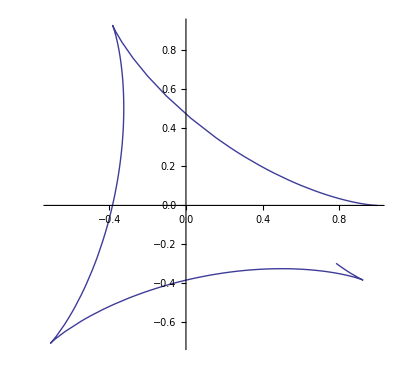
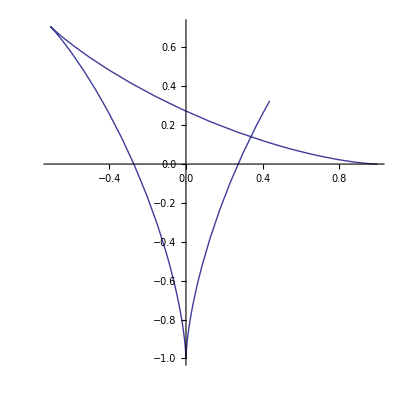
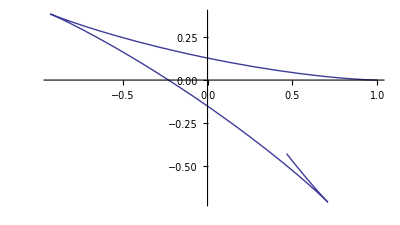
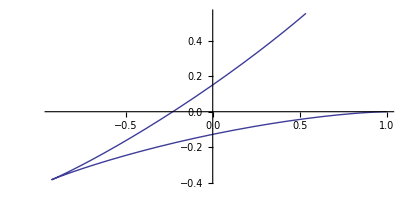
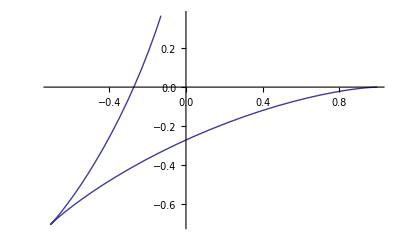
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,2Pi}],{a,{1}},{b,1/16,15/16,1/16}]
```

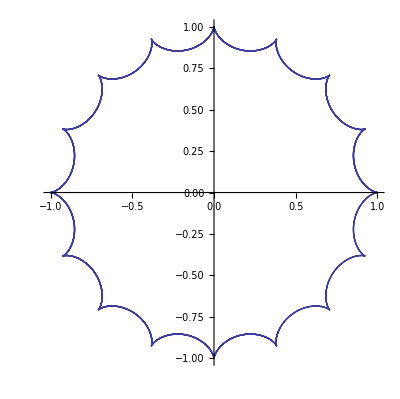
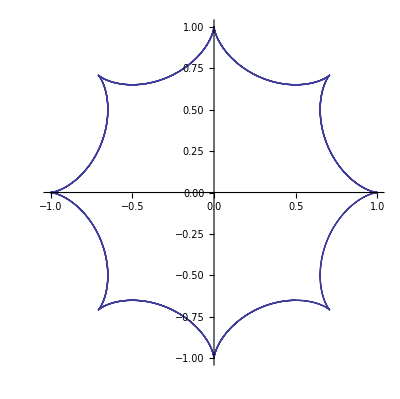
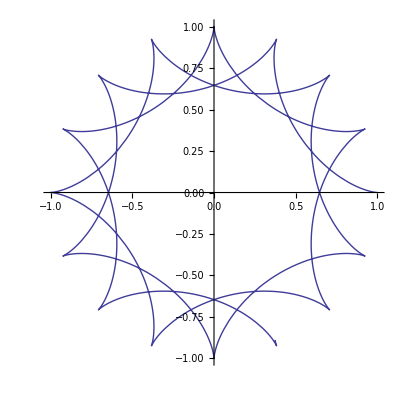
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,17/3 Pi}],{a,{1}},{b,1/16,15/16,1/16}]
```

```mathematica
a=1
b=1/Pi
ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,2*115*Pi}]
```

1

1/π

-Graphics-

```mathematica
a=1
b=3/16
ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,6Pi}]
```

1

3/16

-Graphics-

```mathematica
a=1
b=5/16
ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,10Pi}]
```

1

```mathematica
7/16
```

-Graphics-

```mathematica
Table[ParametricPlot[{(a-b)Cos[u]+b Cos[(a-b)/b u],(a-b)Sin[u]-b Sin[(a-b)/b u]},{u,0,2*3*Pi}],{a,{1}},{b,{1/3,2/3,1/4,3/4}}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

14.6-53

```mathematica
Solve[10^2+100+20*10*1Cos[9t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-π/9},{t→π/9}}

```mathematica
10*Cos[π/9]+Cos[10*π/9]*10
```

0

```mathematica
-10*Sin[π/9]-Sin[10*π/9]*10
```

0

14.5-56

```mathematica
D[{(3 x^2)/(√(9 x^4+1)), 1/(√(9 x^4+1))},x]
```

{-(54 x^5)/((1+9 x^4)^(3/2))+(6 x)/(√(1+9 x^4)),-(18 x^3)/((1+9 x^4)^(3/2))}

```mathematica
{-(54 x^5)/((1+9 x^4)^(3/2))+(6 x)/(√(1+9 x^4)),-(18 x^3)/((1+9 x^4)^(3/2))}*1/(√(9 x^4+1))//Simplify
```

{(6 x)/((1+9 x^4)^2),-(18 x^3)/((1+9 x^4)^2)}

Tech14.1

```mathematica
n=2
ParametricPlot3D[{Cos[2n t]Sin[t],Sin[2n t]Sin[t],Cos[t]},{t,0,π}]
```

2

-Graphics3D-

```mathematica
D[Cos[2n t]Sin[t],t]
D[Sin[2n t]Sin[t],t]
```

Cos[t] Cos[2 n t]-2 n Sin[t] Sin[2 n t]

2 n Cos[2 n t] Sin[t]+Cos[t] Sin[2 n t]

```mathematica
D[Cos[2n t]Sin[t],t]^2+D[Sin[2n t]Sin[t],t]^2//Expand
```

Cos[t]^2 Cos[2 n t]^2+4 n^2 Cos[2 n t]^2 Sin[t]^2+Cos[t]^2 Sin[2 n t]^2+4 n^2 Sin[t]^2 Sin[2 n t]^2

```mathematica
n=12
∫_0^π √(D[Cos[2n t]Sin[t],t]^2+D[Sin[2n t]Sin[t],t]^2+D[Cos[t],t]^2)ⅆt//N
```

12

48.211

15.5-30

```mathematica
Solve[{3 x-4y==-30,4 x+3y==85},{x,y}]
```

{{x→10,y→15}}

```mathematica
6^2+17^2
```

325

15.8-34

```mathematica
D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),{Subscript[u, 1],1}]
```

(3 a (a u_1+b u_2+c u_3)^2)/(u_1 u_2 u_3)-(a u_1+b u_2+c u_3)^3/(u_1^2 u_2 u_3)

```mathematica
Solve[{D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),{Subscript[u, 1],1}]==0,D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),{Subscript[u, 2],1}]==0},{Subscript[u, 1],Subscript[u, 2]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{u_1→(c u_3)/a,u_2→(c u_3)/b},{u_1→-(b u_2)/a-(c u_3)/a},{u_1→-(b u_2)/a-(c u_3)/a},{u_1→-(b u_2)/a-(c u_3)/a},{u_1→-(b u_2)/a-(c u_3)/a}}

```mathematica
D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),{Subscript[u, 1],2}]D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),{Subscript[u, 2],2}]-D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),Subscript[u, 1],Subscript[u, 2]]^2/.{Subscript[u, 1]->(c Subscript[u, 3])/a,Subscript[u, 2]->(c Subscript[u, 3])/b}//Simplify
```

(243 a^4 b^4)/(c^2 u_3^4)

```mathematica
D[(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3]),{Subscript[u, 1],2}]/.{Subscript[u, 1]->(c Subscript[u, 3])/a,Subscript[u, 2]->(c Subscript[u, 3])/b}
```

(18 a^3 b)/(c u_3^2)

```mathematica
(Subscript[u, 1] a+Subscript[u, 2] b+Subscript[u, 3] c)^3/(Subscript[u, 1] Subscript[u, 2] Subscript[u, 3])/.{Subscript[u, 1]->(c Subscript[u, 3])/a,Subscript[u, 2]->(c Subscript[u, 3])/b}//Simplify
```

27 a b c

15.8-46

```mathematica
a=√(8^2+10^2-2*8*10Cos[x])
b=√(10^2+6^2-2*10*6Cos[y])
c=√(6^2+8^2-2*6*8Cos[x+y])
D[a+b+c,{x,1}]
D[a+b+c,{y,1}]
Solve[{D[a+b+c,{x,1}]==0,D[a+b+c,{y,1}]==0},{x,y}]
```

√(164-160 Cos[x])

√(136-120 Cos[y])

√(100-96 Cos[x+y])

(80 Sin[x])/(√(164-160 Cos[x]))+(48 Sin[x+y])/(√(100-96 Cos[x+y]))

(60 Sin[y])/(√(136-120 Cos[y]))+(48 Sin[x+y])/(√(100-96 Cos[x+y]))

```mathematica
2*8*10Sin[x]+2*10*6Sin[y]-2*6*8Sin[x+y]//Simplify
```

8 (20 Sin[x]+15 Sin[y]-12 Sin[x+y])

```mathematica
Solve[{D[2*8*10Sin[x]+2*10*6Sin[y]-2*6*8Sin[x+y],{x,1}]==0,D[2*8*10Sin[x]+2*10*6Sin[y]-2*6*8Sin[x+y],{y,1}]==0},{x,y}]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→0.+0.857811 ⅈ,x→-2.22045×10^-16+0.293165 ⅈ},{y→0.-0.857811 ⅈ,x→2.22045×10^-16-0.293165 ⅈ},{y→-2.0904+1.82756×10^-17 ⅈ,x→-1.95239+2.23346×10^-17 ⅈ},{y→2.0904-1.82756×10^-17 ⅈ,x→1.95239-2.23346×10^-17 ⅈ},{y→-0.688562-2.22045×10^-16 ⅈ,x→0.953147+2.22045×10^-16 ⅈ},{y→0.688562+2.22045×10^-16 ⅈ,x→-0.953147-2.22045×10^-16 ⅈ}}

```mathematica
D[2*8*10Sin[x]+2*10*6Sin[y]-2*6*8Sin[x+y],{x,1}]
D[2*8*10Sin[x]+2*10*6Sin[y]-2*6*8Sin[x+y],{y,1}]
```

160 Cos[x]-96 Cos[x+y]

120 Cos[y]-96 Cos[x+y]

Tech15.2

```mathematica
f[x_,y_]=3x+4y+4
Subscript[x, 0]=1
Subscript[y, 0]=-1
e=0.2
f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]
Plot[f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]],{t,-5,5}]
a[t]=(f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]-f[Subscript[x, 0],Subscript[y, 0]])/e
Plot[(f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]-f[Subscript[x, 0],Subscript[y, 0]])/e,{t,-5,5}]
∫_0^(2π) a[t]ⅆt
```

4+3 x+4 y

1

-1

0.2

4+3 (1+0.2 Cos[t])+4 (-1+0.2 Sin[t])

-Graphics-

5. (1+3 (1+0.2 Cos[t])+4 (-1+0.2 Sin[t]))

-Graphics-

0

```mathematica
f[x_,y_]=x^3+4 y^3
Subscript[x, 0]=1
Subscript[y, 0]=-1
e=0.2
f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]
Plot[f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]],{t,-5,5}]
a[t]=(f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]-f[Subscript[x, 0],Subscript[y, 0]])/e
Plot[(f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]-f[Subscript[x, 0],Subscript[y, 0]])/e,{t,-5,5}]
∫_0^(2π) a[t]ⅆt
```

x^3+4 y^3

1

-1

0.2

(1+0.2 Cos[t])^3+4 (-1+0.2 Sin[t])^3

-Graphics-

5. (3+(1+0.2 Cos[t])^3+4 (-1+0.2 Sin[t])^3)

-Graphics-

-5.65487

```mathematica
f[x_,y_]=x^3+4 y^3
Subscript[x, 0]=1
Subscript[y, 0]=-1
f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]
a[t]=(f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]-f[Subscript[x, 0],Subscript[y, 0]])/e
Table[∫_0^(2π) (f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]-f[Subscript[x, 0],Subscript[y, 0]])/e ⅆt,{e,{0.2,0.02,0.002,0.0002,0.00002}}]
```

x^3+4 y^3

1

-1

(1+0.002 Cos[t])^3+4 (-1+0.002 Sin[t])^3

500. (3+(1+0.002 Cos[t])^3+4 (-1+0.002 Sin[t])^3)

{-5.65487,-0.565487,-0.0565487,-0.00565487,-0.000565487}

```mathematica
f[x_,y_]=x^3+4 y^3
Subscript[x, 0]=1
Subscript[y, 0]=1
e=0.2
Plot[f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]],{t,-5,5}]
Plot3D[f[x,y],{x,-2,2},{y,-2,2},AxesLabel->{x,y,z}]
ParametricPlot3D[{Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t],f[Subscript[x, 0]+e Cos[t],Subscript[y, 0]+e Sin[t]]},{t,-5,5}]
```

x^3+4 y^3

1

1

0.2

-Graphics-

-Graphics3D-

-Graphics3D-

16.8-20

```mathematica
∫_0^π Sin[ϕ]^3 ⅆϕ
```

4/3

Tech16.1

```mathematica
a=1
q=1
∫_(-a/2)^(a/2) ∫_(-a/2)^(a/2) (1/(√(x^2+y^2+q^2)))^3 ⅆxⅆy
```

1

1

4 ArcTan[1/(2 √6)]

```mathematica
Table[2^i,{i,0,9}]
```

{1,2,4,8,16,32,64,128,256,512}

```mathematica
a=1
Table[(q/a^2∫_(-a/2)^(a/2) ∫_(-a/2)^(a/2) (1/(√(x^2+y^2+q^2)))^3 ⅆxⅆy)/(1/q^2),{q,{1,2,4,8,16,32,64,128,256,512}}]//N
```

1

{0.805432,0.94172,0.984654,0.996111,0.999025,0.999756,0.999939,0.999985,0.999996,0.999999}

```mathematica
1/1^2∫_(-a/2)^(a/2) ∫_(-a/2)^(a/2) (1/(√(x^2+y^2+1^2)))^3 ⅆxⅆy
```

4 ArcTan[1/(2 √6)]

```mathematica
a=1
Table[(q/(π (a/2)^2)∫_0^(2π) ∫_0^(a/2) (1/(√(r^2+q^2)))^3 rⅆrⅆθ)/(1/q^2),{q,{1,2,4,8,16,32,64,128,256,512}}]//N
```

1

{0.844582,0.95544,0.988432,0.99708,0.999268,0.999817,0.999954,0.999989,0.999997,0.999999}

Tech16.2

```mathematica
Table[x=RandomReal[{-1,1},1000];y=RandomReal[{-1,1},1000];z=RandomReal[{-1,1},1000];8/1000 Count[x^2+y^2+z^2,x_/;x<1],{i,10}]//N
Mean[%]
4/3 π//N
```

{4.296,3.968,4.208,4.112,4.16,4.04,4.128,4.28,4.248,4.152}

4.1592

4.18879

```mathematica
∫_0^1 2 ρ^2 √(1-ρ^2)ⅆρ
```

π/8

17.2

```mathematica
∫_0^a 2 √2 √(2a x-2 x^2)ⅆx
```

1/2 a √(a^2) π

```mathematica
∫_(-a/(√2))^(a/(√2)) 2 √(a^2-x^2-(a/(√2))^2)ⅆx
```

1/2 a √(a^2) π

17.3-26

```mathematica
D[ArcCot[y/x],x]//Simplify
```

y/(x^2+y^2)

17.7-5

```mathematica
Integrate[2*2 √3 Sin[t]D[2 √3 Cos[t],t]+6*2 √3 Cos[t]D[2 √3 Sin[t],t],{t,2π,0}]
```

-48 π

Tech17.1

```mathematica
Plot3D[{-ⅇ^-y,-ⅇ^(-y+0.1x)},{x,0,3},{y,0,3},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
VectorPlot[{{-1,-ⅇ^-y},{-1,-ⅇ^(-y+0.1x)}},{x,0,2},{y,0,1}]
```

-Graphics-

```mathematica
Manipulate[ParametricPlot[{2 t,2t((1+4α)/2-2α t)},{t,0,1}],{α,-2,2,0.05}]
```

```mathematica
Table[∫_0^1 (D[2t,t]+(Exp[-2t((1+4α)/2-2α t)+0.1*2t])D[2t((1+4α)/2-2α t),t])ⅆt,{α,-2,2,0.05}]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

{3.15242,3.12879,3.10617,3.0845,3.06374,3.04387,3.02483,3.00659,2.98911,2.97237,2.95633,2.94096,2.92624,2.91212,2.89859,2.88563,2.8732,2.86128,2.84985,2.8389,2.82839,2.81832,2.80866,2.79939,2.7905,2.78197,2.77379,2.76594,2.7584,2.75117,2.74423,2.73757,2.73117,2.72503,2.71914,2.71347,2.70803,2.70281,2.69779,2.69297,∫_0^1 (2+ⅇ^(0.2 t-2 (0.5-2.22045×10^-16 t) t) (2 (0.5-2.22045×10^-16 t)-4.44089×10^-16 t))ⅆt,2.68389,2.67961,2.6755,2.75299,2.66774,2.66409,2.66057,2.65719,2.65394,2.65081,2.64781,2.64491,2.64212,2.63944,2.63686,2.63437,2.63197,2.62967,2.62745,2.62531,2.62325,2.62126,2.61934,2.6175,2.61572,2.614,2.61235,2.61075,2.60921,2.60772,2.60629,2.60491,2.60357,2.60228,2.60103,2.59983,2.59867,2.59755,2.59646,2.59541}

```mathematica
1-ⅇ^-1//N
```

0.632121

```mathematica
D[2t,t]+ⅇ^(-2t((1+4α)/2-2α t)+0.1*2t)D[2t((1+4α)/2-2α t),t]//Simplify
```

ⅇ^(t (-1+4 (-1+t) α)) (2 ⅇ^(t (1-4 (-1+t) α))+ⅇ^(0.2 t) (1+(4-8 t) α))

```mathematica
ParametricPlot[{2 t+Sin[2π t],t^2+1-Cos[2π t]},{t,0,1}]
```

-Graphics-

```mathematica
x=2 t+Sin[2π t];
y=t^2+1-Cos[2π t];
∫_0^1 (D[x,t]+(Exp[-y+0.1x])D[y,t])ⅆt//N
```

2.72316

Tech17.2

```mathematica
Manipulate[ParametricPlot3D[{Sin[s]Cos[t],Sin[s]Sin[t],Cos[s]},{t,0,2π},{s,0,(k π)/8}],{k,1,8,1}]
```

```mathematica
Manipulate[ParametricPlot3D[{Sin[s]Cos[t],Sin[s]Sin[t],Cos[s]},{t,0,(k π)/4},{s,0,π}],{k,1,8,1}]
```

```mathematica
ParametricPlot3D[{Sin[s],Cos[s]Sin[t],Sin[t]},{t,0,2π},{s,0,2π},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[s]Cos[t],Sin[s]Sin[t],Cos[t]},{t,0,2π},{s,0,2π},AxesLabel->{x,y,z}]
```

-Graphics3D-

18.3-14

```mathematica
y=(-c/(2B)t+c/(4 B^2)Sin[2B t])Cos[ B t]+(-c/(4 B^2)Cos[2B t])*Sin[B t];
D[y,{t,2}]+B^2 y//Simplify
```

c Sin[B t]

Tech18.2

```mathematica
y=-0.2Cos[√(3/1)t]+0.15/(√(3/1))Sin[√(3/1)t]
dy=D[y,t]
```

-0.2 Cos[√3 t]+0.0866025 Sin[√3 t]

0.15 Cos[√3 t]+0.34641 Sin[√3 t]

```mathematica
y=-0.2Cos[√(3/1)t]+0.15/(√(3/1))Sin[√(3/1)t];
dy=D[y,t];
ParametricPlot[{y,dy},{t,0,(2Pi)/(√(3/1))}]
```

-Graphics-

```mathematica
D[ⅇ^(-α t)(c1* Cos[β t]+c2*Sin[β t]),t]//Simplify
```

ⅇ^(-t α) ((-c1 α+c2 β) Cos[t β]-(c2 α+c1 β) Sin[t β])

```mathematica
q=0.25;(q/1)^2-4*3/1;α=(q/1)/2;β=(√(4*3/1-(q/1)^2))/2;y0=-0.2;v0=0.15;
y=ⅇ^(-α t)(y0* Cos[β t]+(v0+y0*α)/β*Sin[β t])
dy=D[y,t]
ParametricPlot[{y,dy},{t,0,2Pi}]
```

ⅇ^(-0.125 t) (-0.2 Cos[1.72753 t]+0.0723575 Sin[1.72753 t])

-0.125 ⅇ^(-0.125 t) (-0.2 Cos[1.72753 t]+0.0723575 Sin[1.72753 t])+ⅇ^(-0.125 t) (0.125 Cos[1.72753 t]+0.345507 Sin[1.72753 t])

-Graphics-

```mathematica
Manipulate[(q/1)^2-4*3/1;α=(q/1)/2;β=(√(4*3/1-(q/1)^2))/2;y0=-0.2;v0=0.15;y=ⅇ^(-α t)(y0* Cos[β t]+(v0+y0*α)/β*Sin[β t]);
dy=D[y,t];ParametricPlot[{y,dy},{t,0,5Pi}],{q,0,0.5}]
```

```mathematica
t[0]=0;y[0]=-0.2;v[0]=0.15;h=0.1;t[n_]:=t[n-1]+h;
f[x_,y_,z_]:=-3/1 y;
v[n_]:=v[n-1]+h*f[t[n-1],y[n-1],v[n-1]];
y[n_]:=y[n-1]+v[n-1]*h;
ListPlot[Table[{y[n],v[n]},{n,0,50}]]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit will be suppressed during this calculation.

```mathematica
t[n_]:=t[n-1]+h;
f[x_,y_,z_]:=-3/1 y;
v[n_]:=v[n]=v[n-1]+h*f[t[n-1],y[n-1],v[n-1]];
y[n_]:=y[n]=y[n-1]+v[n-1]*h;
t[0]=0;y[0]=-0.2;v[0]=0.15;h=0.1;
ListPlot[Table[{y[n],v[n]},{n,0,100}]]
```

-Graphics-

```mathematica
h=0.02;
t[n_]:=t[n-1]+h;
f[x_,y_,z_]:=-3/1 y;
v[n_]:=v[n]=v[n-1]+h*f[t[n-1],y[n-1],v[n-1]];
y[n_]:=y[n]=y[n-1]+v[n-1]*h;
t[0]=0;y[0]=-0.2;v[0]=0.15;
{y[40],v[40]}
ListPlot[Table[{y[n],v[n]},{n,0,250}]]
```

{0.0493544,0.377087}

-Graphics-

```mathematica
h=0.1;
t[n_]:=t[n-1]+h;
f[x_,y_,z_]:=-3/1 y-0.25/1 z;
v[n_]:=v[n]=v[n-1]+h*f[t[n-1],y[n-1],v[n-1]];
y[n_]:=y[n]=y[n-1]+v[n-1]*h;
t[0]=0;y[0]=-0.2;v[0]=0.15;
ListPlot[Table[{y[n],v[n]},{n,0,100}]]
```

-Graphics-

```mathematica
h=0.02;
t[n_]:=t[n-1]+h;
f[x_,y_,z_]:=-9.8/1 Sin[y];
v[n_]:=v[n]=v[n-1]+h*f[t[n-1],y[n-1],v[n-1]];
y[n_]:=y[n]=y[n-1]+v[n-1]*h;
t[0]=0;y[0]=π/4;v[0]=0;
ListPlot[Table[{t[n],y[n]},{n,0,250}]]
ListPlot[Table[{v[n],y[n]},{n,0,250}]]
```

-Graphics-

-Graphics-

5.5-93

```mathematica
f=2 x^3+3 x^2-36x;D[f,x]//TraditionalForm
```

6 x^2+6 x-36

```mathematica
f1=6 x^2+6 x-36;Plot[f1,{x,-10,10}]
```

-Graphics-

Exa9.5.8

```mathematica
f[x]=In[x] 
(f^(n)(c))/(n!)( x-c)^n
```

THEOREM 5.8

```mathematica
|f^-1(y)-f^-1(a)|≤ϵ    |y-a|≤δ
```

12.7 Kepler’s Laws

```mathematica
(Subscript[r, 0] Subscript[v, 0]^2)/(G M)=(Subscript[v, 0]^2/Subscript[r, 0])/((G M)/Subscript[r, 0]^2)
```

```mathematica
a^(->)=Subscript[r, 0]/(1/κ)((∂s)/(∂t))^2/Subscript[r, 0];Subscript[r, 0]>1/κ
```

```mathematica
Graphics[Circle[{0,0},3],Axes->True]
```